# Mappings between theory and background & Poisson equation for Horndeski theories

```mathematica
Clear["Global`*"];
```

## A) Map between Horndeski G_i to μ, γ_2, γ_3 functions, the 1st, 2nd and 3rd order Poisson modifications as described in Bose & Koyama [1606.02520] . We check for specific theories.

1. Notes

Refer to published versions used for all  Eq. references.

1606.02520 follows the work of Takushima et al 1502.03935 but adds in a mass term to the Continuity and Euler equations to account for scale dependent theories like f(R).

The mass terms M1,M2,M3 of Eq.B4 of 1606.02520 are related to the mass terms M1,M2,M3 of say 0902.0618. We write out this relationship explicitly in what follows.

In both papers, the canonical kinetic energy is defined as  X = -((∂ϕ))^2/2 . In this notebook we assume this.

We write the kinetic term of the Horndeski Lagrangian in Eq.2 of 1502.03935 as G2 in what follows.

A number of typos in 1606.02520 were discovered in creating this notebook. Specifically:

In the first two lines of Eq. B24 we note Π should be ϒ (Π is not defined in the manuscript!)

In Eq. B29, the terms going as k_2^2 and k_3^2 should have a ‘-‘ sign and the last term should have a ‘+‘ as in B.6 of 1502.03935

In Eq. B21, W_(1Q) should have -B_1 G_T^2as it’s first term - compare to A.27 of Takushima

κ = 8 π G_N

2. Takushima et al [1502.03935] functions with mass term included.

#### Useful wave vector functions: k12=|k_1+ k_2| and Eq.41 & Eq.B6 of 1502.03935 multiplied by wave vector magnitudes. Note typo 6.2: B29, ξ_h = xih of 1606.02520.

```mathematica
k12[k1_,k2_,cost_]:=Sqrt[k1^2+k2^2+2k1 k2 cost] 
lambda[k1_,k2_,cost_]:=k1^2k2^2(1- cost^2) 
xih[k1_,k2_,k3_,cos12_,cos13_,cos23_]:=(k1 k2 k3)^2 (1-cos23^2-cos13^2-cos12^2+2cos12 cos13 cos23)
```

#### The time derivatives of the scalar field, chosen such that it is a function of time only.

We will define everything in terms of the background scalar field ϕ[t].

The canonical kinetic term of the scalar field is defined as  X = -((∂ϕ))^2/2 as in 1502.03935

```mathematica
ϕd[t_]:=D[ϕ[t],t];
ϕdd[t_]:=D[ϕ[t],{t,2}]
```

#### Curly functions: A10, A11, A12, A13, A14 of 1502.03935

```mathematica
FT[ϕ_[t_],X_]:=2*(G4[ϕ[t],X]-X*(ϕdd[t]*D[G5[ϕ[t],X],X]+D[G5[ϕ[t],X],ϕ[t]]))

GT[ϕ_[t_],X_]:=2*(G4[ϕ[t],X]-2*X*D[G4[ϕ[t],X],X]-X*(H[t]*ϕd[t]*D[G5[ϕ[t],X],X]-D[G5[ϕ[t],X],ϕ[t]]))

Θ[ϕ_[t_],X_]:=-ϕd[t]*X*D[G3[ϕ[t],X],X]+2*H[t]*G4[ϕ[t],X]-8*H[t]*X*D[G4[ϕ[t],X],X]-8*H[t]*X^2*D[G4[ϕ[t],X],{X,2}]+ϕd[t]*D[G4[ϕ[t],X],ϕ[t]]+2*X*ϕd[t]*D[G4[ϕ[t],X],ϕ[t],X]-H[t]^2*ϕd[t]*(5*X*D[G5[ϕ[t],X],X]+2*X^2*D[G5[ϕ[t],X],{X,2}])+2*H[t]*X*(3*D[G5[ϕ[t],X],ϕ[t]]+2*X*D[G5[ϕ[t],X],ϕ[t],X])

ξ[ϕ_[t_],X_]:=2*X*D[G2[ϕ[t],X],X]-G2[ϕ[t],X]+6*X*ϕd[t]*H[t]*D[G3[ϕ[t],X],X]-2*X*D[G3[ϕ[t],X],ϕ[t]]-6*H[t]^2*G4[ϕ[t],X]+24*H[t]^2*X*(D[G4[ϕ[t],X],X]+X*D[G4[ϕ[t],X],{X,2}])-12*H[t]*X*ϕd[t]*D[G4[ϕ[t],X],ϕ[t],X]-6*H[t]*ϕd[t]*D[G4[ϕ[t],X],ϕ[t]]+2*H[t]^3*X*ϕd[t]*(5*D[G5[ϕ[t],X],X]+2*X*D[G5[ϕ[t],X],{X,2}])-6*H[t]^2*X*(3*D[G5[ϕ[t],X],ϕ[t]]+2*X*D[G5[ϕ[t],X],ϕ[t],X])

𝒫[ϕ_[t_],X_]:=G2[ϕ[t],X]- 2*X*(D[G3[ϕ[t],X],ϕ[t]]+ϕdd[t]*D[G3[ϕ[t],X],X])+
2*(3*H[t]^2+2*D[H[t],t])*G4[ϕ[t],X]-
12*H[t]^2*X*D[G4[ϕ[t],X],X]-
4*H[t]*D[X[t],t]*D[G4[ϕ[t],X],X]-
8*D[H[t],t]*X*D[G4[ϕ[t],X],X]-
8*H[t]*D[X[t],t]*X*D[G4[ϕ[t],X],{X,2}]+
2*(ϕdd[t]+2*H[t]*ϕd[t])*D[G4[ϕ[t],X],ϕ[t]]+
4*X*D[G4[ϕ[t],X],ϕ[t],ϕ[t]]+
4*X*(ϕdd[t]-2*H[t]*ϕd[t])*D[G4[ϕ[t],X],ϕ[t],X]-
2*X*(2*H[t]^3*ϕd[t]+2*H[t]*D[H[t],t]*ϕd[t]+3*H[t]^2*ϕdd[t])*D[G5[ϕ[t],X],X]-
4*H[t]^2*X^2*ϕdd[t]*D[G5[ϕ[t],X],X,X]+
4*H[t]*X*(D[X,t]-H[t]*X)*D[G5[ϕ[t],X],ϕ[t],X]+
2*(2*D[H[t]*X[t],t]+3*H[t]^2*X)*D[G5[ϕ[t],X],ϕ[t]]+
4*H[t]*X*ϕd[t]*D[G5[ϕ[t],X],{ϕ,2}]
```

#### B functions: A4, A5, A6, A7 of 1502.03935

```mathematica
B0[ϕ_[t_],X_]:=X/H[t]*(ϕd[t]*D[G3[ϕ[t],X] ,X]+3(D[X[t],t]+2H[t]X)D[G4[ϕ[t],X],{X,2}] + 2 X D[X[t],t]D[G4[ϕ[t],X],{X,3}]-3ϕd[t] D[G4[ϕ[t],X],ϕ[t],X]+2ϕd[t] X D[G4[ϕ[t],X],ϕ[t],X,X] +(H'[t] + H[t]^2)ϕd[t]D[G5[ϕ[t],X],X] + ϕd[t](2H[t]D[X[t],t]+(H'[t] + H[t]^2)X)D[G5[ϕ[t],X],{X,2}]+H[t]ϕd[t]X D[X[t],t]D[G5[ϕ[t],X],{X,3}]
-2(D[X[t],t]+2H[t]X) D[G5[ϕ[t],X],ϕ[t],X] -  ϕd[t] X D[G5[ϕ[t],X],ϕ[t],ϕ[t],X]  -X(D[X[t],t]-2H[t]X)D[G5[ϕ[t],X],ϕ[t],X,X] )
B1[ϕ_[t_],X_]:=2X(D[G4[ϕ[t],X] ,X] + ϕdd[t](D[G5[ϕ[t],X] ,X] + X D[G5[ϕ[t],X] ,X,X]) -D[G5[ϕ[t],X],ϕ[t]]+ X D[G5[ϕ[t],X],ϕ[t],X])
B2[ϕ_[t_],X_]:=-2X(D[G4[ϕ[t],X] ,X] +2X D[G4[ϕ[t],X] ,{X,2}]  +H[t] ϕd[t]D[G5[ϕ[t],X] ,X] +H[t] ϕd[t] X D[G5[ϕ[t],X] ,{X,2}] -D[G5[ϕ[t],X],ϕ[t]]+ X D[G5[ϕ[t],X],ϕ[t],X])
B3[ϕ_[t_],X_]:=H[t] ϕd[t] X D[G5[ϕ[t],X] ,X]
```

#### C functions: A8, A9 of 1502.03935

```mathematica
C0[ϕ_[t_],X_]:=2 X^2D[G4[ϕ[t],X] ,{X,2}]  + 2X^2/3( 2ϕdd[t]  D[G5[ϕ[t],X] ,{X,2}]+ϕdd[t] X D[G5[ϕ[t],X] ,{X,3}] -2 D[G5[ϕ[t],X] ,ϕ[t],X] +X D[G5[ϕ[t],X] ,ϕ[t],X,X]) 
C1[ϕ_[t_],X_]:=H[t] ϕd[t] X( D[G5[ϕ[t],X] ,X]+X D[G5[ϕ[t],X] ,{X,2}])
```

#### A functions: A1, A2, A3 of 1502.03935 and B.12 of 1606.02520 which introduces the mass term. We also make the transformation X = -1/2 g^μν∂_μ ϕ∂_ν ϕ = 1/2 ϕ'^2 noting the signature (-+++) .

```mathematica
A0[ϕ_[t_],X_]:=D[Θ[ϕ[t],X]/.X->ϕ'[t]^2/2,t]/H[t]^2+Θ[ϕ[t],X]/H[t]+FT[ϕ[t],X]-2*GT[ϕ[t],X]-2*D[GT[ϕ[t],X]/.X->ϕ'[t]^2/2,t]/H[t]-(ξ[ϕ[t],X]+𝒫[ϕ[t],X])/(2*H[t]^2)
A1[ϕ_[t_],X_]:=D[GT[ϕ[t],X]/.X->ϕ'[t]^2/2,t]/H[t]+GT[ϕ[t],X]-FT[ϕ[t],X]
A2[ϕ_[t_],X_]:=GT[ϕ[t],X]-Θ[ϕ[t],X]/H[t]
A0t[ϕ_[t_],X_,k_]:=A0[ϕ[t],X]+ M1t[ϕ[t]]/k^2
```

#### R,T,S,Z functions: A15, A16, A17, A18 of 1502.03935 or B11 of 1606.02520 [Should WE HAVE -A1 A2 in S not + A1 A2 ?]

```mathematica
R[ϕ_[t_],X_,k_]:=A0t[ϕ[t],X,k]*FT[ϕ[t],X]-A1[ϕ[t],X]^2
S[ϕ_[t_],X_,k_]:=A0t[ϕ[t],X,k]*GT[ϕ[t],X]+A1[ϕ[t],X]*A2[ϕ[t],X]
T[ϕ_[t_],X_]:=A1[ϕ[t],X]*GT[ϕ[t],X]+A2[ϕ[t],X]*FT[ϕ[t],X]
Z[ϕ_[t_],X_,k_]:=2*(A0t[ϕ[t],X,k]*GT[ϕ[t],X]^2+2*A1[ϕ[t],X]*A2[ϕ[t],X]*GT[ϕ[t],X]+A2[ϕ[t],X]^2*FT[ϕ[t],X])
```

#### Upsilon functions for 1st order: B8, B9, B10 of 1606.02520

```mathematica
Upphi[ϕ_[t_],X_,k_,a_]:=-k^2/a^2*Z[ϕ[t],X,k]/R[ϕ[t],X,k]
Uppsi[ϕ_[t_],X_,k_,a_]:=-k^2/a^2*Z[ϕ[t],X,k]/S[ϕ[t],X,k] 
Upq[ϕ_[t_],X_,k_,a_]:=-k^2/a^2*Z[ϕ[t],X,k]/T[ϕ[t],X]
```

#### Basic functions for 2nd order (W functions): B17-B22 of 1606.02520 . Note typo 6.3 : W_(1Q)in B21. Compare with A27, κ_Q κ_ψ terms, of 1502.03935

```mathematica
W1phi[ϕ_[t_],X_,k_,a_]:=2 a^2/k^2*(B1[ϕ[t],X]*T[ϕ[t],X]+B3[ϕ[t],X]R[ϕ[t],X,k])/Z[ϕ[t],X,k] 
W2phi[ϕ_[t_],X_,k_,a_]:=2 a^2/k^2*(B2[ϕ[t],X]*T[ϕ[t],X]+B3[ϕ[t],X]S[ϕ[t],X,k])/Z[ϕ[t],X,k]  
W3phi[ϕ_[t_],X_,k_,a_]:=2 a^2/k^2*(B3[ϕ[t],X]T[ϕ[t],X])/Z[ϕ[t],X,k]  
W4phi[ϕ_[t_],X_,k_,a_]:=a^2/k^2*(-2B0[ϕ[t],X]*T[ϕ[t],X]+B1[ϕ[t],X]S[ϕ[t],X,k]+B2[ϕ[t],X]R[ϕ[t],X,k])/Z[ϕ[t],X,k]   
W5phi[ϕ_[t_],X_,k_,a_]:=2 a^2/k^2*T[ϕ[t],X]/Z[ϕ[t],X,k]  

W1psi[ϕ_[t_],X_,k_,a_]:=2 a^2/k^2*(A2[ϕ[t],X]B1[ϕ[t],X]*GT[ϕ[t],X]+B3[ϕ[t],X]S[ϕ[t],X,k])/Z[ϕ[t],X,k]  
W2psi[ϕ_[t_],X_,k_,a_]:=2 a^2/k^2*(A2[ϕ[t],X]B2[ϕ[t],X]*GT[ϕ[t],X]-A2[ϕ[t],X]^2B3[ϕ[t],X])/Z[ϕ[t],X,k]   
W3psi[ϕ_[t_],X_,k_,a_]:=2 a^2/k^2*(A2[ϕ[t],X]B3[ϕ[t],X]GT[ϕ[t],X])/Z[ϕ[t],X,k]   
W4psi[ϕ_[t_],X_,k_,a_]:=a^2/k^2*(-2A2[ϕ[t],X]B0[ϕ[t],X]*GT[ϕ[t],X]-A2[ϕ[t],X]^2B1[ϕ[t],X]+B2[ϕ[t],X]S[ϕ[t],X,k])/Z[ϕ[t],X,k]   
W5psi[ϕ_[t_],X_,k_,a_]:=2 a^2/k^2*(A2[ϕ[t],X]GT[ϕ[t],X])/Z[ϕ[t],X,k]  

W1q[ϕ_[t_],X_,k_,a_]:=2 a^2/k^2*(-B1[ϕ[t],X]*GT[ϕ[t],X]^2+B3[ϕ[t],X]T[ϕ[t],X])/Z[ϕ[t],X,k]   
W2q[ϕ_[t_],X_,k_,a_]:=2 a^2/k^2*(-B2[ϕ[t],X]*GT[ϕ[t],X]^2+A2[ϕ[t],X]B3[ϕ[t],X]GT[ϕ[t],X])/Z[ϕ[t],X,k]   
W3q[ϕ_[t_],X_,k_,a_]:=-2 a^2/k^2*(B3[ϕ[t],X]GT[ϕ[t],X]^2)/Z[ϕ[t],X,k]   
W4q[ϕ_[t_],X_,k_,a_]:=a^2/k^2*(2B0[ϕ[t],X]*GT[ϕ[t],X]^2+A2[ϕ[t],X]B1[ϕ[t],X]GT[ϕ[t],X]+B2[ϕ[t],X]T[ϕ[t],X])/Z[ϕ[t],X,k]    
W5q[ϕ_[t_],X_,k_,a_]:=-2 a^2/k^2*GT[ϕ[t],X]^2/Z[ϕ[t],X,k]
```

#### Basic functions for 3rd order (Z functions): B25-B28 of 1606.02520

```mathematica
Z0[ϕ_[t_],X_,k_,a_]:=2 a^2/k^2*(C1[ϕ[t],X]*T[ϕ[t],X])/Z[ϕ[t],X,k] 
Z1[ϕ_[t_],X_,k_,a_]:=2 a^2/(3k^2)*(3 C0[ϕ[t],X]*T[ϕ[t],X]+C1[ϕ[t],X]*R[ϕ[t],X,k])/Z[ϕ[t],X,k]  
Z2[ϕ_[t_],X_,k_,a_]:=2 a^2/k^2*T[ϕ[t],X]/Z[ϕ[t],X,k]    
Z3[ϕ_[t_],X_,k_,a_]:= B3[ϕ[t],X]  Z2[ϕ[t],X,k,a]
Z4[ϕ_[t_],X_,k_,a_]:=2 a^2/k^2*(B1[ϕ[t],X]*T[ϕ[t],X]+B3[ϕ[t],X]*R[ϕ[t],X,k])/Z[ϕ[t],X,k] 
Z5[ϕ_[t_],X_,k_,a_]:=Z3[ϕ[t],X,k,a]
Z6[ϕ_[t_],X_,k_,a_]:=2 a^2/k^2*(B2[ϕ[t],X]*T[ϕ[t],X]+B3[ϕ[t],X]*S[ϕ[t],X,k])/Z[ϕ[t],X,k]
Z7[ϕ_[t_],X_,k_,a_]:=Z6[ϕ[t],X,k,a]
Z8[ϕ_[t_],X_,k_,a_]:=Z4[ϕ[t],X,k,a]
Z9[ϕ_[t_],X_,k_,a_]:=2 a^2/k^2*(-2 B0[ϕ[t],X]*T[ϕ[t],X]+B1[ϕ[t],X]*S[ϕ[t],X,k]+B2[ϕ[t],X]*R[ϕ[t],X,k])/Z[ϕ[t],X,k] 
Z10[ϕ_[t_],X_,k_,a_]:=2Z2[ϕ[t],X,k,a]
```

#### Gamma2 functions: B16 of 1606.02520 where we have added in a second order mass term

```mathematica
GAM2phi[ϕ_[t_],X_,k_,k1_,k2_,cost_,a_]:=(rho/(a^2 H[t]))^2((W1phi[ϕ[t],X,k,a]/(Uppsi[ϕ[t],X,k1,a]Upq[ϕ[t],X,k2,a])+W2phi[ϕ[t],X,k,a]/(Upphi[ϕ[t],X,k1,a]Upq[ϕ[t],X,k2,a])+W3phi[ϕ[t],X,k,a]/(Uppsi[ϕ[t],X,k1,a]Upphi[ϕ[t],X,k2,a])+W4phi[ϕ[t],X,k,a]/(Upq[ϕ[t],X,k1,a]Upq[ϕ[t],X,k2,a]))lambda[k1,k2,cost]+W5phi[ϕ[t],X,k,a]/(Upq[ϕ[t],X,k1,a]Upq[ϕ[t],X,k2,a])M2t[ϕ[t]])   
GAM2psi[ϕ_[t_],X_,k_,k1_,k2_,cost_,a_]:=(rho/(a^2 H[t]))^2((W1psi[ϕ[t],X,k,a]/(Uppsi[ϕ[t],X,k1,a]Upq[ϕ[t],X,k2,a])+W2psi[ϕ[t],X,k,a]/(Upphi[ϕ[t],X,k1,a]Upq[ϕ[t],X,k2,a])+W3psi[ϕ[t],X,k,a]/(Uppsi[ϕ[t],X,k1,a]Upphi[ϕ[t],X,k2,a])+W4psi[ϕ[t],X,k,a]/(Upq[ϕ[t],X,k1,a]Upq[ϕ[t],X,k2,a]))lambda[k1,k2,cost]+W5psi[ϕ[t],X,k,a]/(Upq[ϕ[t],X,k1,a]Upq[ϕ[t],X,k2,a])M2t[ϕ[t]])   
GAM2q[ϕ_[t_],X_,k_,k1_,k2_,cost_,a_]:=(rho/(a^2 H[t]))^2((W1q[ϕ[t],X,k,a]/(Uppsi[ϕ[t],X,k1,a]Upq[ϕ[t],X,k2,a])+W2q[ϕ[t],X,k,a]/(Upphi[ϕ[t],X,k1,a]Upq[ϕ[t],X,k2,a])+W3q[ϕ[t],X,k,a]/(Uppsi[ϕ[t],X,k1,a]Upphi[ϕ[t],X,k2,a])+W4q[ϕ[t],X,k,a]/(Upq[ϕ[t],X,k1,a]Upq[ϕ[t],X,k2,a]))lambda[k1,k2,cost]+W5q[ϕ[t],X,k,a]/(Upq[ϕ[t],X,k1,a]Upq[ϕ[t],X,k2,a])M2t[ϕ[t]])
```

#### Gamma3 function for phi : single permutation (we exclude the factor of 1/3) of B24 of 1606.02520 . We have also added in a 3rd order mass term M3t. Note typo 6.1 - Π should be ϒ

```mathematica
GAM3phi[ϕ_[t_],X_,k_,k1_,k2_,k3_,cos12_,cos13_,cos23_,a_]:=(1/H[t])(rho/(a^2 H[t]))^3(Z0[ϕ[t],X,k,a]/(Upq[ϕ[t],X,k1,a]Upq[ϕ[t],X,k2,a]Upphi[ϕ[t],X,k3,a])xih[k1,k2,k3,cos12,cos13,cos23]+Z1[ϕ[t],X,k,a]/(Upq[ϕ[t],X,k1,a]Upq[ϕ[t],X,k2,a]Upq[ϕ[t],X,k3,a])xih[k1,k2,k3,cos12,cos13,cos23]+(Z2[ϕ[t],X,k,a]M3t[ϕ[t]])/(Upq[ϕ[t],X,k1,a]Upq[ϕ[t],X,k2,a]Upq[ϕ[t],X,k3,a]))+    
rho(1/(a^2 H[t]))^2(lambda[k1,k12[k2,k3,cos23],(k2 cos12 +  k3 cos13)/ k12[k2,k3,cos23]]((Z3[ϕ[t],X,k,a] GAM2psi[ϕ[t],X,k12[k2,k3,cos23],k2,k3,cos23,a])/Upphi[ϕ[t],X,k1,a]+(Z4[ϕ[t],X,k,a] GAM2psi[ϕ[t],X,k12[k2,k3,cos23],k2,k3,cos23,a])/Upq[ϕ[t],X,k1,a]+(Z5[ϕ[t],X,k,a] GAM2phi[ϕ[t],X,k12[k2,k3,cos23],k2,k3,cos23,a])/Uppsi[ϕ[t],X,k1,a](Z6[ϕ[t],X,k,a] GAM2phi[ϕ[t],X,k12[k2,k3,cos23],k2,k3,cos23,a])/Upq[ϕ[t],X,k1,a]+(Z7[ϕ[t],X,k,a] GAM2q[ϕ[t],X,k12[k2,k3,cos23],k2,k3,cos23,a])/Upphi[ϕ[t],X,k1,a]+(Z8[ϕ[t],X,k,a] GAM2q[ϕ[t],X,k12[k2,k3,cos23],k2,k3,cos23,a])/Uppsi[ϕ[t],X,k1,a]+(Z9[ϕ[t],X,k,a] GAM2q[ϕ[t],X,k12[k2,k3,cos23],k2,k3,cos23,a])/Upq[ϕ[t],X,k1,a])+ (Z10[ϕ[t],X,k,a] M2t[ϕ[t]] GAM2q[ϕ[t],X,k12[k2,k3,cos23],k2,k3,cos23,a])/Upq[ϕ[t],X,k1,a] )
```

#### Poisson equation functions: B30,B31,B32 of 1606.02520

```mathematica
rho=3 H0^2 Om0/(κ a^3);
mu[ϕ_[t_],X_,k_,a_]:=-k^2/a^2*2/κ*1/Upphi[ϕ[t],X,k,a]
gam2[ϕ_[t_],X_,k_,k1_,k2_,cost_,a_]:=-(k/(a H[t]))^2 GAM2phi[ϕ[t],X,k,k1,k2,cost,a]
gam3[ϕ_[t_],X_,k_,k1_,k2_,k3_,cos12_,cos13_,cos23_,a_]:=-(k/(a H[t]))^2 1/3(GAM3phi[ϕ[t],X,k,k1,k2,k3,cos12,cos13,cos23,a]+GAM3phi[ϕ[t],X,k,k3,k1,k2,cos13,cos23,cos12,a]+GAM3phi[ϕ[t],X,k,k2,k3,k1,cos23,cos12,cos13,a])
```

3. First Order  (μ )

## LCDM

```mathematica
Clear[G2,G3,G4,G5,M1,ϕ,M1t];
G2[ϕ_[t_],X_]:=-Λ;
G3[ϕ_[t_],X_]:=0;
G4[ϕ_[t_],X_]:=1/(2 κ);
G5[ϕ_[t_],X_]:=0;
M1t[ϕ_[t_]]:= 0;
```

```mathematica
FullSimplify[mu[ϕ[t],X,k,a]]
```

1

## Hu Sawicki f(R) gravity : See Eq. 2.32 of 1606.02520

```mathematica
Clear[G2,G3,G4,G5,M1,R0,Rb,fRR,ϕ,fofr,Rbf,M1t];
G2[ϕ_[t_],X_]:=V[ϕ[t]];
G3[ϕ_[t_],X_]:=0;
G4[ϕ_[t_],X_]:= (1+ϕ[t])/(2 κ);
G5[ϕ_[t_],X_]:=0;
```

We find the following relation between M1 of 0902.0618 and M1t as written in Equations of motion

```mathematica
M1t[ϕ_[t_]]:=M1 * ((ϕ'[t] a)/(2 H[t]))^2 1/κ
```

```mathematica
FullSimplify[mu[ϕ[t],X,k,a]/. ϕ[t]->0]
```

1+k^2/(3 k^2-a^2 M1)

### Calculate value of M1

#### Start with the Ricci scalar (see Eq.3.88 and 3.89 of 1802.00989) and define the background Ricci assuming a LCDM background, and f_R assuming R>>m^2. [ Eq. 3.87 of 1802.00989]

```mathematica
Clear[Rb,fR,RoffR,Rf,M1]
```

```mathematica
RoffR[fr]:=Rb0  Sqrt[fR0/fr]
Rf=Simplify[D[RoffR[fr],fr]]
```

-(√(fR0/fr) Rb0)/(2 fr)

```mathematica
Rb[a_]:=3H0^2 * (Om0 + 4 a^3 (1-Om0))/ a^3 ;
fR[a_]:=fR0*(Rb[1]/Rb[a])^2;
```

```mathematica
M1=FullSimplify[PowerExpand[Rf/.{fr->fR[a],Rb0->Rb[1]}]]
```

-(3 H0^2 (-4 a^3 (-1+Om0)+Om0)^3)/(2 a^9 fR0 (4-3 Om0)^2)

## Cubic Galileon / DGP

```mathematica
Clear[G2,G3,G4,G5,M1,R0,Rb,fRR,Rf,ϕ,M1t];
G2[ϕ_[t_],X_]:=X/κ;
G3[ϕ_[t_],X_]:=2X/κ/Λ0^2;
G4[ϕ_[t_],X_]:=1/(2 κ);
G5[ϕ_[t_],X_]:=0;
M1t[ϕ_[t_]]:=0;
```

```mathematica
FullSimplify[mu[ϕ[t],X,k,a]/. X->ϕ'[t]^2/2]
```

1+(2 ϕ'[t]^4)/(Λ0^4+8 Λ0^2 H[t] ϕ'[t]-2 ϕ'[t]^4+4 Λ0^2 ϕ''[t])

```mathematica
FullSimplify[mu[ϕ[t],X,k,a]/. X->ϕ'[t]^2/2]/.{H[t]->H[a],ϕ'[t]->a H[a] ϕ'[a] , ϕ''[t]->a H[a]( H[a] ϕ'[a] + a H'[a]ϕ'[a] + a H[a] ϕ''[a])}/.{ϕ'[a]->1,ϕ''[a]->0}
```

1+(2 a^4 H[a]^4)/(Λ0^4+8 a Λ0^2 H[a]^2-2 a^4 H[a]^4+4 a Λ0^2 H[a] (H[a]+a H'[a]))

```mathematica
beta[a_]:=1+H[a]/Orc*(1+a H'[a]/(3H[a]))
FullSimplify[Solve[(2 a^4 H[a]^4)/(Λ0^4+8 a Λ0^2 H[a]^2-2 a^4 H[a]^4+4 a Λ0^2 H[a] (H[a]+a H'[a])) - 1/(3 beta[a]) ==0 /.{Λ0^2->L2,Λ0^4->0}, L2]]
```

{{L2→(a^3 H[a]^3 (4 Orc+3 H[a]+a H'[a]))/(6 Orc H[a]+2 a Orc H'[a])}}

## KGB model : consistency check with 1502.03935

```mathematica
Clear[G2,G3,G4,G5,M1,R0,Rb,fRR,ϕ,M1t];
G2[ϕ_[t_],X_]:=-X;
G3[ϕ_[t_],X_]:=(rc^2 X  κ)^n/Sqrt[κ];
G4[ϕ_[t_],X_]:=1/(2 κ);
G5[ϕ_[t_],X_]:=0;
M1t[ϕ_[t_]]:=0;
```

#### Check with Appendix E of 1502.03935

```mathematica
A0tak =Simplify[ X/H[t]^2 -  2 n /Sqrt[κ] * (rc^2 κ^2)^n ( 2 ϕ'[t]/H[t] + n  ϕ''[t]/H[t]^2)X^n /. X->ϕ'[t]^2/2]
```

(ϕ'[t]^2-(2^(2-n) n (rc^2 κ^2)^n (ϕ'[t]^2)^n (2 H[t] ϕ'[t]+n ϕ''[t]))/(√κ))/(2 H[t]^2)

```mathematica
A0ben = FullSimplify[A0t[ϕ[t],X,k]/. X->ϕ'[t]^2/2]
```

(ϕ'[t]^2-(2^(2-n) n (rc^2 κ ϕ'[t]^2)^n (2 H[t] ϕ'[t]+n ϕ''[t]))/(√κ))/(2 H[t]^2)

```mathematica
FullSimplify[A0tak/A0ben]
```

(2^n √κ ϕ'[t]^2-4 n (rc^2 κ^2)^n (ϕ'[t]^2)^n (2 H[t] ϕ'[t]+n ϕ''[t]))/(2^n √κ ϕ'[t]^2-4 n (rc^2 κ ϕ'[t]^2)^n (2 H[t] ϕ'[t]+n ϕ''[t]))

### Attractor solution : Compare with Eq. E12-E20 of 1502.03935 and Eq. 104.

```mathematica
D[G3[ϕ[t],X],X]
```

n rc^2 √κ (rc^2 X κ)^(-1+n)

```mathematica
FullSimplify[(1/(3 H[t] n rc^2 κ^(1/2)) * (rc^2 κ/2)^(1-n))^(1/(2n-1))] (*phi'*)
```

3^(1/(1-2 n)) ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(1/(-1+2 n))

```mathematica
step0=FullSimplify[ mu[ϕ[t],X,k,a]/. X-> ϕ'[t]^2/2] (*Sub X *)
```

(2^n (2^n √κ ϕ'[t]^2-4 n (rc^2 κ ϕ'[t]^2)^n (2 H[t] ϕ'[t]+n ϕ''[t])))/(4^n √κ ϕ'[t]^2+2 n^2 √κ ϕ'[t]^2 (rc^2 κ ϕ'[t]^2)^(2 n)-2^(2+n) n (rc^2 κ ϕ'[t]^2)^n (2 H[t] ϕ'[t]+n ϕ''[t]))

```mathematica
step1=FullSimplify[step0/.ϕ''[t]->-1/(2n-1)ϕ'[t]H'[t]/H[t]](*Sub phi'' -> Eq.E12 *)
```

(2^n (2^n √κ ϕ'[t]-(4 n (2 H[t]^2+(n H'[t])/(1-2 n)) (rc^2 κ ϕ'[t]^2)^n)/H[t]))/(-(2^(2+n) n ((-2+4 n) H[t]^2-n H'[t]) (rc^2 κ ϕ'[t]^2)^n)/((-1+2 n) H[t])+√κ ϕ'[t] (4^n+2 n^2 (rc^2 κ ϕ'[t]^2)^(2 n)))

```mathematica
step2=FullSimplify[step1/.ϕ'[t] ->3^(1/(1-2 n)) ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(1/(-1+2 n))/.H'[t]->-H[t]^2(2n-1)3Om/(2(2n-Om))] (*Sub H' -> Eq.E13 *)
```

(2^n (2^n 3^(1/(1-2 n)) √κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(1/(-1+2 n))-(2 n (-4 Om+n (8+3 Om)) (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^n H[t])/(2 n-Om)))/(3^(1/(1-2 n)) √κ (4^n+2 n^2 (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^(2 n)) ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(1/(-1+2 n))-(2^(1+n) n (-4 Om+n (8+3 Om)) (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^n H[t])/(2 n-Om))

```mathematica
step3=Simplify[PowerExpand[step2]]
```

(n^(2/(-1+2 n)) ((3^(1/(1-2 n))-4 9^(n/(1-2 n))) Om+n (-2 3^(1/(1-2 n))+8 9^(n/(1-2 n))+3^(1/(1-2 n)) Om)) rc^((8 n^2)/(-1+2 n)))/(n^(2/(-1+2 n)) ((3^(1/(1-2 n))-4 9^(n/(1-2 n))) Om+n (-2 3^(1/(1-2 n))+8 9^(n/(1-2 n))+3^(1/(1-2 n)) Om)) rc^((8 n^2)/(-1+2 n))+2^(1/(1-2 n)) 3^((1+4 n)/(1-2 n)) (-2 n+Om) rc^(4 n) H[t]^((4 n)/(1-2 n)))

```mathematica
step4=Simplify[step3/.rc -> 1/H0 *(2^(n-1)/(3n))^(1/(2n))(1/(6(1-(Om H[t]^2 a^3/H0^2))))^((2n-1)/(4n))](*Sub rc Eq.103 *)
```

(n^(2/(-1+2 n)) ((3^(1/(1-2 n))-4 9^(n/(1-2 n))) Om+n (-2 3^(1/(1-2 n))+8 9^(n/(1-2 n))+3^(1/(1-2 n)) Om)) ((3^(-(1+2 n)/(4 n)) (2^(-1+n)/n)^(1/2/n) (H0^2/(2 H0^2-2 a^3 Om H[t]^2))^(1/2-1/(4 n)))/H0)^((8 n^2)/(-1+2 n)))/(2^(1/(1-2 n)) 3^((1+4 n)/(1-2 n)) (-2 n+Om) H[t]^((4 n)/(1-2 n)) ((3^(-(1+2 n)/(4 n)) (2^(-1+n)/n)^(1/2/n) (H0^2/(2 H0^2-2 a^3 Om H[t]^2))^(1/2-1/(4 n)))/H0)^(4 n)+n^(2/(-1+2 n)) ((3^(1/(1-2 n))-4 9^(n/(1-2 n))) Om+n (-2 3^(1/(1-2 n))+8 9^(n/(1-2 n))+3^(1/(1-2 n)) Om)) ((3^(-(1+2 n)/(4 n)) (2^(-1+n)/n)^(1/2/n) (H0^2/(2 H0^2-2 a^3 Om H[t]^2))^(1/2-1/(4 n)))/H0)^((8 n^2)/(-1+2 n)))

```mathematica
Simplify[-2/(2n-1)-2]
```

(4 n)/(1-2 n)

```mathematica
numerator=Simplify[PowerExpand[Numerator[step4]]]/.{H[t]^((4 n)/(1-2 n))-> (1-Om)/(1-Om0) H0^((4 n)/(1-2 n)),H0^2-a^3 Om H[t]^2-> H0^2(1-Om0)}
denominator=Simplify[PowerExpand[Denominator[step4]]]/.{H[t]^((4 n)/(1-2 n))-> (1-Om)/(1-Om0) H0^((4 n)/(1-2 n)),H0^2-a^3 Om H[t]^2-> H0^2(1-Om0)}
```

(3^(-(2 n (1+2 n))/(-1+2 n)) 4^(n/(1-2 n)) H0^((4 n)/(1-2 n)) ((3^(1/(1-2 n))-4 9^(n/(1-2 n))) Om+n (-2 3^(1/(1-2 n))+8 9^(n/(1-2 n))+3^(1/(1-2 n)) Om)) (H0^2 (1-Om0))^(-2 n))/n^2

(4^(n/(1-2 n)) (3^(-(4 n (1+n))/(-1+2 n)) H0^((4 n)/(1-2 n)) (1-Om) (-2 n+Om)+3^(-(2 n (1+2 n))/(-1+2 n)) H0^((4 n)/(1-2 n)) ((3^(1/(1-2 n))-4 9^(n/(1-2 n))) Om+n (-2 3^(1/(1-2 n))+8 9^(n/(1-2 n))+3^(1/(1-2 n)) Om))) (H0^2 (1-Om0))^(-2 n))/n^2

```mathematica
step5=FullSimplify[numerator/denominator]
```

(4+(3^(1/(1-2 n)) (n (-6+Om)+Om))/(3^(1/(1-2 n)) n+9^(n/(1-2 n)) (2 n-Om)))/Om

```mathematica
Simplify[1/(1-2 n)-(2 n)/(1-2 n)]
```

1

```mathematica
step6=Simplify[(4+(3 (n (-6+Om)+Om))/(3 n+ (2 n-Om)))/Om]
```

(Om-n (2+3 Om))/(Om (-5 n+Om))

```mathematica
Loft = -3/2 H^2 Om step6  ;
Lt = -3/2H^2 (2n+(3n-1)Om )/(5n-Om);
```

```mathematica
FullSimplify[Loft-Lt]
```

0

4. Second Order (γ_2)

## LCDM

```mathematica
Clear[G2,G3,G4,G5,M1t,M2t,M1,M2,ϕ];
G2[ϕ_[t_],X_]:=-Λ;
G3[ϕ_[t_],X_]:=0;
G4[ϕ_[t_],X_]:=1/(2 κ);
G5[ϕ_[t_],X_]:=0;
M1t[ϕ_[t_]]:= 0;
M2t[ϕ_[t_]]:= 0;
```

```mathematica
Simplify[gam2[ϕ[t],X,k,k1,k2,cost,a]]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

0

## Hu Sawicki f(R) gravity : See Eq. 2.38 of 1606.02520

```mathematica
Clear[G2,G3,G4,G5,M1,M2,R0,Rb,fRR,ϕ,fofr,Rbf,Rf,Rff,M1,M1t,M2t,M2];
G2[ϕ_[t_],X_]:=V[ϕ[t]];
G3[ϕ_[t_],X_]:=0;
G4[ϕ_[t_],X_]:=(1+ϕ[t])/(2 κ);
G5[ϕ_[t_],X_]:=0;
```

We find the following relation between M1 & M2 of 0902.0618 and M1t as written in Equations of motion

```mathematica
M1t[ϕ_[t_]]:=M1 * (ϕ'[t]/2)^2 a^2/(κ H[t]^2)     
M2t[ϕ_[t_]]:=M2 * (ϕ'[t]/2)^3 a^4/(κ  H[t])
```

#### Find forms for M1, M2 according to 0902.0618

```mathematica
Clear[Rb,fR,RoffR,Rf,Rff,M1f,M2f]
```

```mathematica
RoffR[fr]:=Rb0  Sqrt[fR0/fr]
Rf=Simplify[D[RoffR[fr],fr]]
Rff=Simplify[D[RoffR[fr],{fr,2}]]
```

-(√(fR0/fr) Rb0)/(2 fr)

(3 √(fR0/fr) Rb0)/(4 fr^2)

```mathematica
Rb[a_]:=3H0^2 * (Om0 + 4 a^3 (1-Om0))/ a^3 ;
fR[a_]:=fR0*(Rb[1]/Rb[a])^2;
```

```mathematica
M1f=FullSimplify[PowerExpand[Rf/.{fr->fR[a],Rb0->Rb[1]}]]
M2f=FullSimplify[PowerExpand[Rff/.{fr->fR[a],Rb0->Rb[1]}]]
```

-(3 H0^2 (-4 a^3 (-1+Om0)+Om0)^3)/(2 a^9 fR0 (4-3 Om0)^2)

(9 H0^2 (-4 a^3 (-1+Om0)+Om0)^5)/(4 a^15 fR0^2 (4-3 Om0)^4)

#### Check value of gamma2

```mathematica
FullSimplify[gam2[ϕ[t],X,k,k1,k2,cost,a]/.{ ϕ[t]->0}]
```

-(9 H0^4 k^2 M2 Om0^2)/(4 a^2 (-3 k^2+a^2 M1) (-3 k1^2+a^2 M1) (-3 k2^2+a^2 M1) H[t]^2)

## Cubic Galileon / DGP

```mathematica
Clear[G2,G3,G4,G5,M1,R0,Rb,fRR,ϕ,M1t];
G2[ϕ_[t_],X_]:=X/κ;
G3[ϕ_[t_],X_]:=2X/κ/Λ0^2;
G4[ϕ_[t_],X_]:=1/(2 κ);
G5[ϕ_[t_],X_]:=0;
M1t[ϕ_[t_]]:=0;
M2t[ϕ_[t_]]:=0;
```

```mathematica
Simplify[gam2[ϕ[t],X,k,k1,k2,cost,a]/. {X->ϕ'[t]^2/2}]
```

(18 (-1+cost^2) H0^4 Om0^2 Λ0^4 ϕ'[t]^6)/(a^6 H[t]^2 (Λ0^4+8 Λ0^2 H[t] ϕ'[t]-2 ϕ'[t]^4+4 Λ0^2 ϕ''[t])^3)

## KGB model : consistency check with 1502.03935

```mathematica
Clear[G2,G3,G4,G5,M1,R0,Rb,fRR,ϕ,M1t];
G2[ϕ_[t_],X_]:=-X;
G3[ϕ_[t_],X_]:=(rc^2 X  κ)^n/Sqrt[κ];
G4[ϕ_[t_],X_]:=1/(2 κ);
G5[ϕ_[t_],X_]:=0;
M1t[ϕ_[t_]]:=0;
M2t[ϕ_[t_]]:=0;
```

#### Check Nγ = -H^2 γ2/(1-μ^2) (Eq.108 of 1502.03935)

```mathematica
D[G3[ϕ[t],X],X]
```

n rc^2 √κ (rc^2 X κ)^(-1+n)

```mathematica
FullSimplify[(1/(3 H[t] n rc^2 κ^(1/2)) * (rc^2 κ/2)^(1-n))^(1/(2n-1))] (*phi'*)
```

3^(1/(1-2 n)) ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(1/(-1+2 n))

```mathematica
FullSimplify[(-H[t]^2)/(1-cost^2)gam2[ϕ[t],X,k,k1,k2,cost,a]/.k->k12[k1,k2,cost]/. X-> ϕ'[t]^2/2](*Sub X *)
```

-(9 2^(1+2 n) H0^4 n^4 Om0^2 √κ ϕ'[t]^4 (rc^2 κ ϕ'[t]^2)^(4 n))/(a^6 (4^n √κ ϕ'[t]^2+2 n^2 √κ ϕ'[t]^2 (rc^2 κ ϕ'[t]^2)^(2 n)-2^(2+n) n (rc^2 κ ϕ'[t]^2)^n (2 H[t] ϕ'[t]+n ϕ''[t]))^3)

```mathematica
FullSimplify[-(2^(1+2 n) n^4 rho^2 κ^(5/2) ϕ'[t]^4 (rc^2 κ ϕ'[t]^2)^(4 n))/((4^n √κ ϕ'[t]^2+2 n^2 √κ ϕ'[t]^2 (rc^2 κ ϕ'[t]^2)^(2 n)-2^(2+n) n (rc^2 κ ϕ'[t]^2)^n (2 H[t] ϕ'[t]+n ϕ''[t]))^3)/.ϕ''[t]->-1/(2n-1)ϕ'[t]H'[t]/H[t]](*Sub phi'' -> Eq.E12 *)
```

-(9 2^(1+2 n) H0^4 n^4 Om0^2 √κ ϕ'[t] (rc^2 κ ϕ'[t]^2)^(4 n))/(a^6 (-(2^(2+n) n ((-2+4 n) H[t]^2-n H'[t]) (rc^2 κ ϕ'[t]^2)^n)/((-1+2 n) H[t])+√κ ϕ'[t] (4^n+2 n^2 (rc^2 κ ϕ'[t]^2)^(2 n)))^3)

```mathematica
FullSimplify[-(2^(1+2 n) n^4 rho^2 κ^(5/2) ϕ'[t] (rc^2 κ ϕ'[t]^2)^(4 n))/((-(2^(2+n) n ((-2+4 n) H[t]^2-n H'[t]) (rc^2 κ ϕ'[t]^2)^n)/((-1+2 n) H[t])+√κ ϕ'[t] (4^n+2 n^2 (rc^2 κ ϕ'[t]^2)^(2 n)))^3)/.ϕ'[t] ->3^(1/(1-2 n)) ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(1/(-1+2 n))/.H'[t]->-H[t]^2(2n-1)3Om/(2(2n-Om))] (*Sub H' -> Eq.E13 *)
```

-(2^(1+2 n) 3^(2+1/(1-2 n)) H0^4 n^4 (2 n-Om)^3 Om0^2 √κ (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^(4 n) ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(1/(-1+2 n)))/(a^6 (3^(1/(1-2 n)) (2 n-Om) √κ (4^n+2 n^2 (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^(2 n)) ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(1/(-1+2 n))-2^(1+n) n (-4 Om+n (8+3 Om)) (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^n H[t])^3)

```mathematica
FullSimplify[PowerExpand[2^(1+2 n) 3^(1/(1-2 n)) n^4 (2 n-Om)^3 rho^2 κ^(5/2) (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^(4 n) ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(1/(-1+2 n))]]
```

(2^((2+(7-12 n) n)/(1-2 n)) 3^((3+4 n)/(1-2 n)) H0^4 n^(5/(1-2 n)) (2 n-Om)^3 Om0^2 rc^((10 n)/(1-2 n)) H[t]^((1+8 n)/(1-2 n)))/a^6

```mathematica
FullSimplify[PowerExpand[2^(1+n) n (-4 Om+n (8+3 Om)) (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^n H[t]]]
```

2^((1+n-4 n^2)/(1-2 n)) 9^(n/(1-2 n)) n^(1/(1-2 n)) (-4 Om+n (8+3 Om)) rc^((2 n)/(1-2 n)) H[t]^(1/(1-2 n))

```mathematica
FullSimplify[PowerExpand[3^(1/(1-2 n)) (2 n-Om) √κ (4^n+2 n^2 (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^(2 n)) ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(1/(-1+2 n))]]
```

2^((1+n-4 n^2)/(1-2 n)) 3^(1/(1-2 n)) n^(1/(1-2 n)) (2 n-Om) rc^((n (2+8 n))/(1-2 n)) H[t]^(1/(1-2 n)) (rc^((8 n^2)/(-1+2 n))+2^(1/(1-2 n)) 81^(n/(1-2 n)) n^(2/(1-2 n)) rc^(4 n) H[t]^((4 n)/(1-2 n)))

```mathematica
FullSimplify[2^((1+n-4 n^2)/(1-2 n)) 3^(1/(1-2 n)) n^(1/(1-2 n)) (2 n-Om) rc^((n (2+8 n))/(1-2 n)) H[t]^(1/(1-2 n)) (rc^((8 n^2)/(-1+2 n))+2^(1/(1-2 n)) 81^(n/(1-2 n)) n^(2/(1-2 n)) rc^(4 n) H[t]^((4 n)/(1-2 n)))-2^((1+n-4 n^2)/(1-2 n)) 9^(n/(1-2 n)) n^(1/(1-2 n)) (-4 Om+n (8+3 Om)) rc^((2 n)/(1-2 n)) H[t]^(1/(1-2 n))]
```

2^((1+n-4 n^2)/(1-2 n)) n^(1/(1-2 n)) rc^((2 n)/(1-2 n)) H[t]^(1/(1-2 n)) (9^(n/(1-2 n)) (4 Om-n (8+3 Om))+3^(1/(1-2 n)) (2 n-Om) (1+2^(1/(1-2 n)) 81^(n/(1-2 n)) n^(2/(1-2 n)) rc^((4 n)/(1-2 n)) H[t]^((4 n)/(1-2 n))))

```mathematica
Simplify[-(2^((2+(7-12 n) n)/(1-2 n)) 3^((1+8 n)/(1-2 n)) n^(5/(1-2 n)) (2 n-Om)^3 rc^((10 n)/(1-2 n)) rho^2 κ^2 H[t]^((1+8 n)/(1-2 n)))/((2^((1+n-4 n^2)/(1-2 n)) n^(1/(1-2 n)) rc^((2 n)/(1-2 n)) H[t]^(1/(1-2 n)) (3^((2n)/(1-2 n)) (4 Om-n (8+3 Om))+3^(1/(1-2 n)) (2 n-Om) (1+2^(1/(1-2 n)) 81^(n/(1-2 n)) n^(2/(1-2 n)) rc^((4 n)/(1-2 n)) H[t]^((4 n)/(1-2 n)))))^3)]
```

-(2^((1-4 n)/(-1+2 n)) 3^((3+4 n)/(1-2 n)) H0^4 n^(2/(1-2 n)) (2 n-Om)^3 Om0^2 rc^((4 n)/(1-2 n)) H[t]^((2-8 n)/(-1+2 n)))/(a^6 (9^(n/(1-2 n)) (4 Om-n (8+3 Om))+3^(1/(1-2 n)) (2 n-Om) (1+2^(1/(1-2 n)) 81^(n/(1-2 n)) n^(2/(1-2 n)) rc^((4 n)/(1-2 n)) H[t]^((4 n)/(1-2 n))))^3)

```mathematica
Simplify[(1+8 n)/(1-2 n)-(6n)/(1-2 n)]
```

(1+2 n)/(1-2 n)

```mathematica
(2^((1-4 n)/(-1+2 n)) 3^((1+2 n)/(1-2 n)) n^(2/(1-2 n)) (2 n-Om)^3 rc^((4 n)/(1-2 n)) rho^2 κ^2 H[t]^((2-8 n)/(-1+2 n)))/((  Om-n (2+3 Om)+3 (2 n-Om) 2^(1/(1-2 n)) 3^((4n)/(1-2 n)) n^(2/(1-2 n)) rc^((4 n)/(1-2 n)) H[t]^((4 n)/(1-2 n)))^3) (*Manual reductions*)
```

(2^((1-4 n)/(-1+2 n)) 3^(2+(1+2 n)/(1-2 n)) H0^4 n^(2/(1-2 n)) (2 n-Om)^3 Om0^2 rc^((4 n)/(1-2 n)) H[t]^((2-8 n)/(-1+2 n)))/(a^6 (Om-n (2+3 Om)+2^(1/(1-2 n)) 3^(1+(4 n)/(1-2 n)) n^(2/(1-2 n)) (2 n-Om) rc^((4 n)/(1-2 n)) H[t]^((4 n)/(1-2 n)))^3)

```mathematica
FullSimplify[(2^((1-4 n)/(-1+2 n)) 3^((1+2 n)/(1-2 n)) n^(2/(1-2 n)) (2 n-Om)^3 rc^((4 n)/(1-2 n)) rho^2 κ^2 H[t]^((2-8 n)/(-1+2 n)))/((  Om-n (2+3 Om)+3 (2 n-Om) 2^(1/(1-2 n)) 3^((4n)/(1-2 n)) n^(2/(1-2 n)) rc^((4 n)/(1-2 n)) H[t]^((4 n)/(1-2 n)))^3)/.rc -> 1/H0 *(2^(n-1)/(3n))^(1/(2n))(1/(6(1-(Om H[t]^2 a^3/H0^2))))^((2n-1)/(4n))](*Sub rc Eq.103 *)
```

(3^(1+2/(1-2 n)) H0^4 n^(2/(1-2 n)) (2 n-Om)^3 Om0^2 H[t]^(2+4/(-1+2 n)) ((2^(1/4/n) 3^(-(1+2 n)/(4 n)) (2^(-1+n)/n)^(1/2/n) (H0^2/(H0^2-a^3 Om H[t]^2))^(1/2-1/(4 n)))/H0)^((4 n)/(1-2 n)))/(2 a^6 ((Om-n (2+3 Om)) H[t]^((4 n)/(-1+2 n))+2 3^(1+(4 n)/(1-2 n)) n^(2/(1-2 n)) (2 n-Om) ((2^(-1/4/n) 3^(-(1+2 n)/(4 n)) (2^n/n)^(1/2/n) (H0^2/(H0^2-a^3 Om H[t]^2))^(1/2-1/(4 n)))/H0)^((4 n)/(1-2 n)))^3)

```mathematica
FullSimplify[PowerExpand[3^((1+2 n)/(1-2 n)) n^(2/(1-2 n)) (2 n-Om)^3 rho^2 κ^2 H[t]^(2+4/(-1+2 n)) ((2^(1/4/n) 3^(-(1+2 n)/(4 n)) (2^(-1+n)/n)^(1/2/n) (H0^2/(H0^2-a^3 Om H[t]^2))^(1/2-1/(4 n)))/H0)^((4 n)/(1-2 n))]]
```

(9 H0^(4+2/(-1+2 n)) (2 n-Om)^3 Om0^2 H[t]^(2+4/(-1+2 n)) (H0^2-a^3 Om H[t]^2))/(2 a^6)

```mathematica
FullSimplify[PowerExpand[2 ((Om-n (2+3 Om)) H[t]^((4 n)/(-1+2 n))+2 3^(1+(4 n)/(1-2 n)) n^(2/(1-2 n)) (2 n-Om) ((2^(-1/4/n) 3^(-(1+2 n)/(4 n)) (2^n/n)^(1/2/n) (H0^2/(H0^2-a^3 Om H[t]^2))^(1/2-1/(4 n)))/H0)^((4 n)/(1-2 n)))^3]]
```

2 ((Om-n (2+3 Om)) H[t]^((4 n)/(-1+2 n))+H0^(2/(-1+2 n)) (2 n-Om) (H0^2-a^3 Om H[t]^2))^3

```mathematica
Simplify[-2/(2n-1)-2]
```

(4 n)/(1-2 n)

```mathematica
Simplify[4+4/(-1+2 n)]
```

(8 n)/(-1+2 n)

```mathematica
FullSimplify[(1/2 H0^(2/(-1+2 n)) (2 n-Om)^3 rho^2 κ^2 H[t]^(2+4/(-1+2 n)) (H0^2-a^3 Om H[t]^2))/(2 ((Om-n (2+3 Om)) H[t]^((4 n)/(-1+2 n))+H0^(2/(-1+2 n)) (2 n-Om) (H0^2-a^3 Om H[t]^2))^3)](*Substitute for rho kappa*)
```

(9 H0^(4+2/(-1+2 n)) (2 n-Om)^3 Om0^2 H[t]^(2+4/(-1+2 n)) (H0^2-a^3 Om H[t]^2))/(4 a^6 ((Om-n (2+3 Om)) H[t]^((4 n)/(-1+2 n))+H0^(2/(-1+2 n)) (2 n-Om) (H0^2-a^3 Om H[t]^2))^3)

```mathematica
gam2f=-(9(2 n-Om)^3 H[t]^2)/4(1-Om)/(Om( 5n-Om  )^3) ;(*Reduced using Eq.102 and definition of Om(a)*)
```

```mathematica
Ngam = -9/4((1-Om)(2n-Om)^3)/(Om(5n-Om)^3)H[t]^2;
```

```mathematica
FullSimplify[gam2f-Ngam]
```

0

5. Third Order (γ_3)

## LCDM

```mathematica
Clear[G2,G3,G4,G5,M1t,M2t,M1,M2,ϕ];
G2[ϕ_[t_],X_]:=-Λ;
G3[ϕ_[t_],X_]:=0;
G4[ϕ_[t_],X_]:=1/(2 κ);
G5[ϕ_[t_],X_]:=0;
M1t[ϕ_[t_]]:= 0;
M2t[ϕ_[t_]]:= 0;
M3t[ϕ_[t_]]:= 0;
```

```mathematica
Simplify[gam3[ϕ[t],X,k,k1,k2,k3,cos12,cos13,cos23,a]]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

0

## Hu Sawicki f(R) gravity

```mathematica
Clear[G2,G3,G4,G5,M1,M2,R0,Rb,fRR,ϕ,fofr,Rbf,Rf,Rff,Rfff,M1,M1t,M2t,M3t,M2];
G2[ϕ_[t_],X_]:=V[ϕ[t]];
G3[ϕ_[t_],X_]:=0;
G4[ϕ_[t_],X_]:=(1+ϕ[t])/(2 κ);
G5[ϕ_[t_],X_]:=0;
```

We find the following relation between M1, M2 & M3 of 0902.0618 and M1t as written in Equations of motion

```mathematica
M1t[ϕ_[t_]]:=M1 * 1/κ(ϕ'[t]/2)^2 a^2/H[t]^2     
M2t[ϕ_[t_]]:=M2 *  1/κ(ϕ'[t]/2)^3 a^4/H[t]   
M3t[ϕ_[t_]]:=M3 * 1/κ(ϕ'[t]/2)^4  a^6(2/3)
```

#### Find forms for M1, M2, M3 according to 0902.0618

```mathematica
Clear[Rb,fR,RoffR,Rf,Rff,Rfff,M1f,M2f]
```

```mathematica
RoffR[fr]:=Rb0  Sqrt[fR0/fr]
Rf=Simplify[D[RoffR[fr],fr]]
Rff=Simplify[D[RoffR[fr],{fr,2}]]
Rfff=Simplify[D[RoffR[fr],{fr,3}]]
```

-(√(fR0/fr) Rb0)/(2 fr)

(3 √(fR0/fr) Rb0)/(4 fr^2)

-(15 √(fR0/fr) Rb0)/(8 fr^3)

```mathematica
Rb[a_]:=3H0^2 * (Om0 + 4 a^3 (1-Om0))/ a^3 ;
fR[a_]:=fR0*(Rb[1]/Rb[a])^2;
```

```mathematica
M1f=FullSimplify[PowerExpand[Rf/.{fr->fR[a],Rb0->Rb[1]}]]
M2f=FullSimplify[PowerExpand[Rff/.{fr->fR[a],Rb0->Rb[1]}]]
M3f=FullSimplify[PowerExpand[Rfff/.{fr->fR[a],Rb0->Rb[1]}]]
```

-(3 H0^2 (-4 a^3 (-1+Om0)+Om0)^3)/(2 a^9 fR0 (4-3 Om0)^2)

(9 H0^2 (-4 a^3 (-1+Om0)+Om0)^5)/(4 a^15 fR0^2 (4-3 Om0)^4)

(45 H0^2 (4 a^3 (-1+Om0)-Om0)^7)/(8 a^21 fR0^3 (4-3 Om0)^6)

#### Check value of gamma3 (unsymmetrized)

```mathematica
FullSimplify[Series[FullSimplify[-(k/(a H[t]))^2 GAM3phi[ϕ[t],X,k,k1,k2,k3,cos12,cos13,cos23,a]/.{ ϕ[t]->0}]/.{(-3 (k2^2+2 cos23 k2 k3+k3^2)+a^2 M1)-> -Pik23 a^2*3,(-3 k1^2+a^2 M1)-> -Pik1 a^2*3,(-3 k2^2+a^2 M1)-> -Pik2 a^2*3,(-3 k3^2+a^2 M1)-> -Pik3 a^2*3,(-3 k^2+a^2 M1)->-Pik a^2*3},{M3,0,1}]/.{(-3 k2^2-6 cos23 k2 k3-3 k3^2+a^2 M1)->  -Pik23 a^2*3}/.{M2->M2f}]
```

(9 H0^10 k^2 Om0^3 (-4 a^3 (-1+Om0)+Om0)^10)/(64 a^41 fR0^4 (4-3 Om0)^8 Pik Pik1 Pik2 Pik23 Pik3 H[t]^2)+(H0^6 k^2 Om0^3 M3)/(36 a^11 Pik Pik1 Pik2 Pik3 H[t]^2)+O[M3]^2

```mathematica
FullSimplify[%/.{M3->M3f}]
```

SeriesData::sdatv: First argument (45 H0^2 (4 a^3 (-1+Om0)-Om0)^7)/(8 a^21 fR0^3 (4-3 Om0)^6) is not a valid variable.

(9 H0^10 k^2 Om0^3 (-4 a^3 (-1+Om0)+Om0)^10)/(64 a^41 fR0^4 (4-3 Om0)^8 Pik Pik1 Pik2 Pik23 Pik3 H[t]^2)+(H0^6 k^2 Om0^3 45 H0^2 (4 a^3 (-1+Om0)-Om0)^7)/(36 a^11 Pik Pik1 Pik2 Pik3 H[t]^2 8 a^21 fR0^3 (4-3 Om0)^6)+O[(45 H0^2 (4 a^3 (-1+Om0)-Om0)^7)/(8 a^21 fR0^3 (4-3 Om0)^6)]^2

## Cubic Galileon / DGP

```mathematica
Clear[G2,G3,G4,G5,M1,R0,Rb,fRR,ϕ,M1t];
G2[ϕ_[t_],X_]:=X/κ;
G3[ϕ_[t_],X_]:=2X/κ/Λ0^2;
G4[ϕ_[t_],X_]:=1/(2 κ);
G5[ϕ_[t_],X_]:=0;
M1t[ϕ_[t_]]:=0;
M2t[ϕ_[t_]]:=-2 rc^2/a^4 k1^2 k2^2 (1-cost^2) *(1/κ)(1/H[t])^3(ϕ'[t]/2)^3(a^2 H[t])^2     (*Using the same rescaling as f(R)*)
M3t[ϕ_[t_]]:=0;
```

```mathematica
FullSimplify[gam3[ϕ[t],X,k,k1,k2,k3,cos12,cos13,cos23,a]/.rc^2->1/(4 H0^2 Orc)]
```

-((rho^3 X^4 κ^3 Λ0^8 ϕ'[t]^6 (32 H0^2 (k1^2+2 cos12 k1 k2+k2^2-(cos13 k1+cos23 k2)^2) k3^2 (k1^2+2 cos13 k1 k3+k3^2) (k2^2+2 cos23 k2 k3+k3^2) Orc X (-32 (-1+cos12^2) H0^2 Orc X-(-1+cost^2) Λ0^2 ϕ'[t]^2)+(1-cost^2) k1^2 k2^2 (k1^2+2 cos13 k1 k3+k3^2) (k2^2+2 cos23 k2 k3+k3^2) Λ0^2 ϕ'[t]^2 (-32 (-1+cos12^2) H0^2 Orc X-(-1+cost^2) Λ0^2 ϕ'[t]^2)+32 H0^2 (k1^2+2 cos12 k1 k2+k2^2) (k1^2+2 cos13 k1 k3+k3^2) (k2^2+2 cos23 k2 k3+k3^2-(cos12 k2+cos13 k3)^2) Orc X (-32 (-1+cos23^2) H0^2 k3^2 Orc X-(-1+cost^2) k1^2 Λ0^2 ϕ'[t]^2)+(1-cost^2) k2^2 (k1^2+2 cos12 k1 k2+k2^2) (k1^2+2 cos13 k1 k3+k3^2) Λ0^2 ϕ'[t]^2 (-32 (-1+cos23^2) H0^2 k3^2 Orc X-(-1+cost^2) k1^2 Λ0^2 ϕ'[t]^2)+32 H0^2 (k1^2+2 cos12 k1 k2+k2^2) (k2^2+2 cos23 k2 k3+k3^2) (k1^2+2 cos13 k1 k3+k3^2-(cos12 k1+cos23 k3)^2) Orc X (-32 (-1+cos13^2) H0^2 k3^2 Orc X-(-1+cost^2) k2^2 Λ0^2 ϕ'[t]^2)+(1-cost^2) k1^2 (k1^2+2 cos12 k1 k2+k2^2) (k2^2+2 cos23 k2 k3+k3^2) Λ0^2 ϕ'[t]^2 (-32 (-1+cos13^2) H0^2 k3^2 Orc X-(-1+cost^2) k2^2 Λ0^2 ϕ'[t]^2)))/(24 H0^4 (k1^2+2 cos12 k1 k2+k2^2) k3^2 (k1^2+2 cos13 k1 k3+k3^2) (k2^2+2 cos23 k2 k3+k3^2) Orc^2 H[t]^2 (-2 X Λ0^4+8 X ϕ'[t] (-2 Λ0^2 H[t]+X ϕ'[t])+2 Λ0^2 (2 X-3 ϕ'[t]^2) ϕ''[t])^3 (X Λ0^4-4 X ϕ'[t] (-2 Λ0^2 H[t]+X ϕ'[t])+Λ0^2 (-2 X+3 ϕ'[t]^2) ϕ''[t])^2))

## KGB model : consistency check with 1502.03935

```mathematica
Clear[G2,G3,G4,G5,M1,R0,Rb,fRR,ϕ,M1t];
G2[ϕ_[t_],X_]:=-X;
G3[ϕ_[t_],X_]:=(rc^2 X  κ)^n/Sqrt[κ];
G4[ϕ_[t_],X_]:=1/(2 κ);
G5[ϕ_[t_],X_]:=0;
M1t[ϕ_[t_]]:=0;
M2t[ϕ_[t_]]:=0;
M3t[ϕ_[t_]]:=0;
```

#### Check H^2μ_Φ (λ=0) = Eq.106 of 1502.03935 = -γ_3 (without permutations and without lambda(k) and without k )

```mathematica
κphi=-rho/H[t]^2 1/Upphi[ϕ[t],X,1,1];
κpsi=-rho/H[t]^2 1/Uppsi[ϕ[t],X,1,1];
κq=-rho/H[t]^2 1/Upq[ϕ[t],X,1,1];
λphi = -2/7 κphi λ + λx/Z[ϕ[t],X,k](2B0[ϕ[t],X]T[ϕ[t],X] κq^2-3B1[ϕ[t],X]S[ϕ[t],X,k] κq^2-3B2[ϕ[t],X]R[ϕ[t],X,k] κq^2-6B3[ϕ[t],X]R[ϕ[t],X,k]κq κpsi);
λpsi = -2/7 κpsi λ + λx/Z[ϕ[t],X,k](2B0[ϕ[t],X]A2[ϕ[t],X]GT[ϕ[t],X] κq^2+B1[ϕ[t],X](A2[ϕ[t],X]^2 κq^2-2A2[ϕ[t],X]GT[ϕ[t],X]κq κpsi)-B2[ϕ[t],X](S[ϕ[t],X,k] κq^2+2A2[ϕ[t],X]GT[ϕ[t],X]κq κphi)-2B3[ϕ[t],X](S[ϕ[t],X,k]κq κpsi-A2[ϕ[t],X]^2 κq κphi+A2[ϕ[t],X]GT[ϕ[t],X]κpsi κphi));
λq = -2/7 κq λ - λx/Z[ϕ[t],X,k](2B0[ϕ[t],X] GT[ϕ[t],X]^2 κq^2+B1[ϕ[t],X](A2[ϕ[t],X]GT[ϕ[t],X] κq^2-2 GT[ϕ[t],X]^2 κq κpsi)+B2[ϕ[t],X](T[ϕ[t],X] κq^2-2 GT[ϕ[t],X]^2 κq κphi)+2B3[ϕ[t],X](S[ϕ[t],X,k]κq κpsi+A2[ϕ[t],X]GT[ϕ[t],X]κq κphi-GT[ϕ[t],X]^2 κpsi κphi));
μphi =2/Z[ϕ[t],X,k](2B0[ϕ[t],X] T[ϕ[t],X]κq λq-2B1[ϕ[t],X]S[ϕ[t],X,k]κq λq-B1[ϕ[t],X] T[ϕ[t],X]κq λpsi-2B2[ϕ[t],X]R[ϕ[t],X,k]κq λq-B2[ϕ[t],X]T[ϕ[t],X]κq λphi -2B3[ϕ[t],X]R[ϕ[t],X,k]κpsi λq -2B3[ϕ[t],X]R[ϕ[t],X,k]κq λpsi-2B3[ϕ[t],X]S[ϕ[t],X,k]κq λphi);
```

```mathematica
λ=0;
λx=1;
Clear[rho]
```

```mathematica
T1=Simplify[H[t]^2 μphi]
```

-(2^(-2+5 n) n^6 rho^3 κ^(7/2) (rc^2 X κ)^(6 n) ϕ'[t]^6)/((2^n X √κ-2^(2+n) n (rc^2 X κ)^n H[t] ϕ'[t]+2^n n^2 √κ (rc^2 X κ)^(2 n) ϕ'[t]^2+2^n n (rc^2 X κ)^n ϕ''[t]-n (rc^2 κ ϕ'[t]^2)^n ϕ''[t]-2 n^2 (rc^2 κ ϕ'[t]^2)^n ϕ''[t])^5)

```mathematica
T2=Simplify[-3(k/a)^2 GAM3phi[ϕ[t],X,k,k1,k2,k3,cos12,cos13,cos23,a]*k1^2 k2^2 k3^2 (k2^2+2 cos23 k2 k3+k3^2)]
```

-(2^(-2+5 n) n^6 rho^3 κ^(7/2) (rc^2 X κ)^(6 n) ϕ'[t]^6)/((2^n X √κ-2^(2+n) n (rc^2 X κ)^n H[t] ϕ'[t]+2^n n^2 √κ (rc^2 X κ)^(2 n) ϕ'[t]^2+2^n n (rc^2 X κ)^n ϕ''[t]-n (rc^2 κ ϕ'[t]^2)^n ϕ''[t]-2 n^2 (rc^2 κ ϕ'[t]^2)^n ϕ''[t])^5)

```mathematica
Simplify[T1/T2]
```

1

#### Check KGB case

```mathematica
Clear[rho,λ,λx]
λx=1;
```

```mathematica
D[G3[ϕ[t],X],X]
```

n rc^2 √κ (rc^2 X κ)^(-1+n)

```mathematica
FullSimplify[(1/(3 H[t] n rc^2 κ^(1/2)) * (rc^2 κ/2)^(1-n))^(1/(2n-1))] (*phi'*)
```

3^(1/(1-2 n)) ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(1/(-1+2 n))

```mathematica
Simplify[H[t]^2 μphi/.{X-> ϕ'[t]^2/2 }](*Sub X *) ;
```

```mathematica
Simplify[%/.ϕ''[t]->-1/(2n-1)ϕ'[t]H'[t]/H[t]](*Sub phi'' -> Eq.E12 *) ;
```

```mathematica
Simplify[%/.ϕ'[t] ->3^(1/(1-2 n)) ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(1/(-1+2 n))/.H'[t]->-H[t]^2(2n-1)3Om/(2(2n-Om))] (*Sub H' -> Eq.E13 *)
```

-((2^(3+2 n) 3^(1/(1-2 n)) n^4 rho^2 κ^(5/2) (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^(4 n) ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(1/(-1+2 n)) (9^(1/(1-2 n)) κ λ (4^n+2 n^2 (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^(2 n))^2 ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n))-(2^(2+n) 3^(1/(1-2 n)) n (-4 Om+n (8+3 Om)) √κ λ (4^n+2 n^2 (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^(2 n)) (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^n ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(1/(-1+2 n)) H[t])/(2 n-Om)+(4^n n^2 (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^(2 n) (7 (-2 n+Om)^2 rho κ+4 (-4 Om+n (8+3 Om))^2 λ H[t]^2))/(-2 n+Om)^2))/(7 (3^(1/(1-2 n)) √κ (4^n+2 n^2 (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^(2 n)) ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(1/(-1+2 n))-(2^(1+n) n (-4 Om+n (8+3 Om)) (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^n H[t])/(2 n-Om))^5))

```mathematica
T1=Simplify[PowerExpand[-(2^(3+2 n) 3^(1/(1-2 n)) n^4 rho^2 κ^(5/2) (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^(4 n) ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(1/(-1+2 n)) (2 n-Om)^-2(9^(1/(1-2 n)) κ λ (4^n+2 n^2 (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^(2 n))^2 ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n))(2 n-Om)^2-2^(2+n) 3^(1/(1-2 n)) n (-4 Om+n (8+3 Om)) √κ λ (4^n+2 n^2 (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^(2 n))(2 n-Om) (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^n ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(1/(-1+2 n)) H[t]+4^n n^2 (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^(2 n) (7 (-2 n+Om)^2 rho κ+4 (-4 Om+n (8+3 Om))^2 λ H[t]^2)))]]
```

-1/(-2 n+Om)^2 2^((4+3 n-12 n^2)/(1-2 n)) 3^((1+8 n)/(1-2 n)) n^(5/(1-2 n)) rc^((10 n)/(1-2 n)) rho^2 κ^2 H[t]^((1+8 n)/(1-2 n)) (2^((2 n (-3+4 n))/(-1+2 n)) 81^(n/(1-2 n)) n^(2/(1-2 n)) rc^((4 n)/(1-2 n)) H[t]^((4 n)/(1-2 n)) (7 (-2 n+Om)^2 rho κ+4 (-4 Om+n (8+3 Om))^2 λ H[t]^2)+2^((2 (-1+n))/(-1+2 n)) 9^(1/(1-2 n)) n^(2/(1-2 n)) (-2 n+Om)^2 rc^(-(4 n (1+4 n))/(-1+2 n)) λ H[t]^(2/(1-2 n)) (4^n rc^((8 n^2)/(-1+2 n))+2^(1+(4 (-1+n) n)/(-1+2 n)) 81^(n/(1-2 n)) n^(2/(1-2 n)) rc^(4 n) H[t]^((4 n)/(1-2 n)))^2-2^((-3+2 n+4 n^2)/(-1+2 n)) 3^((1+2 n)/(1-2 n)) n^(2/(1-2 n)) (2 n-Om) (-4 Om+n (8+3 Om)) rc^((4 n)/(1-2 n)) λ H[t]^(2/(1-2 n)) (4^n+2^(1+(4 (-1+n) n)/(-1+2 n)) 81^(n/(1-2 n)) n^(2/(1-2 n)) rc^((4 n)/(1-2 n)) H[t]^((4 n)/(1-2 n))))

```mathematica
T2=Simplify[PowerExpand[(7 (2 n-Om)^-5(3^(1/(1-2 n)) √κ (4^n+2 n^2 (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^(2 n)) ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(1/(-1+2 n))(2 n-Om)-2^(1+n) n (-4 Om+n (8+3 Om)) (9^(1/(1-2 n)) rc^2 κ ((2^(-1+n) √κ (rc^2 κ)^-n)/(n H[t]))^(2/(-1+2 n)))^n H[t])^5)]]
```

(7 2^((5 (-1+n))/(-1+2 n)) n^(5/(1-2 n)) H[t]^(5/(1-2 n)) (4^n 9^(n/(1-2 n)) (4 Om-n (8+3 Om)) rc^((2 n)/(1-2 n))+3^(1/(1-2 n)) (2 n-Om) rc^(-(2 n (1+4 n))/(-1+2 n)) (4^n rc^((8 n^2)/(-1+2 n))+2^(1+(4 (-1+n) n)/(-1+2 n)) 81^(n/(1-2 n)) n^(2/(1-2 n)) rc^(4 n) H[t]^((4 n)/(1-2 n))))^5)/(2 n-Om)^5

```mathematica
Simplify[T1/T2]
```

-((2^(-1+6 n) 3^((1+8 n)/(1-2 n)) (2 n-Om)^5 rc^((10 n)/(1-2 n)) rho^2 κ^2 (2^((2 n (-3+4 n))/(-1+2 n)) 81^(n/(1-2 n)) n^(2/(1-2 n)) rc^((4 n)/(1-2 n)) H[t]^((4 n)/(1-2 n)) (7 (-2 n+Om)^2 rho κ+4 (-4 Om+n (8+3 Om))^2 λ H[t]^2)+2^((2 (-1+n))/(-1+2 n)) 9^(1/(1-2 n)) n^(2/(1-2 n)) (-2 n+Om)^2 rc^(-(4 n (1+4 n))/(-1+2 n)) λ H[t]^(2/(1-2 n)) (4^n rc^((8 n^2)/(-1+2 n))+2^(1+(4 (-1+n) n)/(-1+2 n)) 81^(n/(1-2 n)) n^(2/(1-2 n)) rc^(4 n) H[t]^((4 n)/(1-2 n)))^2-2^((-3+2 n+4 n^2)/(-1+2 n)) 3^((1+2 n)/(1-2 n)) n^(2/(1-2 n)) (2 n-Om) (-4 Om+n (8+3 Om)) rc^((4 n)/(1-2 n)) λ H[t]^(2/(1-2 n)) (4^n+2^(1+(4 (-1+n) n)/(-1+2 n)) 81^(n/(1-2 n)) n^(2/(1-2 n)) rc^((4 n)/(1-2 n)) H[t]^((4 n)/(1-2 n)))))/(7 (-2 n+Om)^2 H[t]^4 (4^n 9^(n/(1-2 n)) (4 Om-n (8+3 Om)) rc^((2 n)/(1-2 n))+3^(1/(1-2 n)) (2 n-Om) rc^(-(2 n (1+4 n))/(-1+2 n)) (4^n rc^((8 n^2)/(-1+2 n))+2^(1+(4 (-1+n) n)/(-1+2 n)) 81^(n/(1-2 n)) n^(2/(1-2 n)) rc^(4 n) H[t]^((4 n)/(1-2 n))))^5))

```mathematica
4
```

```mathematica
Simplify[4 n-(8 n^2)/(-1+2 n)]
```

(4 n)/(1-2 n)

```mathematica
FullSimplify[((4 Om-n (8+3 Om)) +3(2 n-Om)  (1 +2^(1/(1-2 n)) 3^((4n)/(1-2 n)) n^(2/(1-2 n)) rc^((4 n)/(1-2 n)) H[t]^((4 n)/(1-2 n))))^2-((4 Om-n (8+3 Om))^2 +3^2 (2 n-Om)^2   ( 1+2^(1/(1-2 n)) 3^((4n)/(1-2 n)) n^(2/(1-2 n)) rc^((4 n)/(1-2 n)) H[t]^((4 n)/(1-2 n)))^2+2 3  (2 n-Om) (4 Om-n (8+3 Om))  (1+2^(1/(1-2 n)) 3^((4n)/(1-2 n)) n^(2/(1-2 n)) rc^((4 n)/(1-2 n)) H[t]^((4 n)/(1-2 n))))]
```

```mathematica
T11=-(2^((1-14 n+20 n^2)/(-1+2 n)) 3^((1+12 n)/(1-2 n)) (2 n-Om)^5 rc^((14 n)/(1-2 n)) rho^2 κ^2 n^(2/(1-2 n))H[t]^((4 n)/(1-2 n)) ( 7 (-2 n+Om)^2 rho κ+4λ H[t]^2((4 Om-n (8+3 Om)) +3(2 n-Om)  (1 +2^(1/(1-2 n)) 3^((4n)/(1-2 n)) n^(2/(1-2 n)) rc^((4 n)/(1-2 n)) H[t]^((4 n)/(1-2 n))))^2));
T22=(7 (-2 n+Om)^2 H[t]^4 2^(10n) 3^((10n)/(1-2 n)) rc^((10n)/(1-2 n))((4 Om-n (8+3 Om)) +3(2 n-Om)  (1 +2^(1/(1-2 n)) 3^((4n)/(1-2 n)) n^(2/(1-2 n)) rc^((4 n)/(1-2 n)) H[t]^((4 n)/(1-2 n))))^5);
```

```mathematica
Simplify[T11/T22]
```

-(2^((1-4 n)/(-1+2 n)) 3^((1+2 n)/(1-2 n)) n^(2/(1-2 n)) (2 n-Om)^5 rc^((4 n)/(1-2 n)) rho^2 κ^2 H[t]^(-4+(4 n)/(1-2 n)) (7 (-2 n+Om)^2 rho κ+4 λ H[t]^2 (Om-n (2+3 Om)+2^(1/(1-2 n)) 3^(1+(4 n)/(1-2 n)) n^(2/(1-2 n)) (2 n-Om) rc^((4 n)/(1-2 n)) H[t]^((4 n)/(1-2 n)))^2))/(7 (-2 n+Om)^2 (Om-n (2+3 Om)+2^(1/(1-2 n)) 3^(1+(4 n)/(1-2 n)) n^(2/(1-2 n)) (2 n-Om) rc^((4 n)/(1-2 n)) H[t]^((4 n)/(1-2 n)))^5)

```mathematica
Simplify[-(2^((1-4 n)/(-1+2 n)) 3^((1+2 n)/(1-2 n)) n^(2/(1-2 n)) (2 n-Om)^5 rc^((4 n)/(1-2 n)) rho^2 κ^2 H[t]^(-4+(4 n)/(1-2 n)) (7 (-2 n+Om)^2 rho κ+4 λ H[t]^2 (Om-n (2+3 Om)+2^(1/(1-2 n)) 3^(1+(4 n)/(1-2 n)) n^(2/(1-2 n)) (2 n-Om) rc^((4 n)/(1-2 n)) H[t]^((4 n)/(1-2 n)))^2))/(7 (-2 n+Om)^2 (Om-n (2+3 Om)+2^(1/(1-2 n)) 3^(1+(4 n)/(1-2 n)) n^(2/(1-2 n)) (2 n-Om) rc^((4 n)/(1-2 n)) H[t]^((4 n)/(1-2 n)))^5)/.rc -> 1/H0 *(2^(n-1)/(3n))^(1/(2n))(1/(6(1-(Om H[t]^2 a^3/H0^2))))^((2n-1)/(4n))](*Sub rc Eq.103 *)
```

-((2^((1-4 n)/(-1+2 n)) 3^((1+2 n)/(1-2 n)) n^(2/(1-2 n)) (2 n-Om)^5 rho^2 κ^2 H[t]^(-4+(4 n)/(1-2 n)) ((3^(-(1+2 n)/(4 n)) (2^(-1+n)/n)^(1/2/n) (H0^2/(2 H0^2-2 a^3 Om H[t]^2))^(1/2-1/(4 n)))/H0)^((4 n)/(1-2 n)) (7 (-2 n+Om)^2 rho κ+4 λ H[t]^2 (Om-n (2+3 Om)+2^(1/(1-2 n)) 3^(1+(4 n)/(1-2 n)) n^(2/(1-2 n)) (2 n-Om) H[t]^((4 n)/(1-2 n)) ((3^(-(1+2 n)/(4 n)) (2^(-1+n)/n)^(1/2/n) (H0^2/(2 H0^2-2 a^3 Om H[t]^2))^(1/2-1/(4 n)))/H0)^((4 n)/(1-2 n)))^2))/(7 (-2 n+Om)^2 (Om-n (2+3 Om)+2^(1/(1-2 n)) 3^(1+(4 n)/(1-2 n)) n^(2/(1-2 n)) (2 n-Om) H[t]^((4 n)/(1-2 n)) ((3^(-(1+2 n)/(4 n)) (2^(-1+n)/n)^(1/2/n) (H0^2/(2 H0^2-2 a^3 Om H[t]^2))^(1/2-1/(4 n)))/H0)^((4 n)/(1-2 n)))^5))

```mathematica
Simplify[-2/(2n-1)-2]
```

(4 n)/(1-2 n)

```mathematica
Simplify[-((2 n-Om)^3 rho^2 κ^2  ( 1- a^3 Om (H[t]/H0)^2)(H[t]/H0)^((4 n)/(1-2 n)) (7 (-2 n+Om)^2 rho κ+4λ H[t]^2 (Om-n (2+3 Om)+  (2 n-Om) (H[t]/H0)^((4 n)/(1-2 n)) (1- a^3 Om (H[t]/H0)^2))^2))/(7 2^2 H[t]^4(Om-n (2+3 Om)+(2 n-Om) (H[t]/H0)^((4 n)/(1-2 n)) (1- a^3 Om (H[t]/H0)^2))^5)/.{(H[t]/H0)^((4 n)/(1-2 n))->(1-Om)/(1-Om0),1- a^3 Om (H[t]/H0)^2->(1-Om0),rho-> 3 H0^2 Om0/(κ a^3)}]
```

(9 H0^4 (-1+Om) (-2 n+Om)^3 Om0^2 (21 H0^2 (-2 n+Om)^2 Om0+4 a^3 Om^2 (-5 n+Om)^2 λ H[t]^2))/(28 a^9 (5 n-Om)^5 Om^5 H[t]^4)

```mathematica
finalmu=(9 (-1+Om) (-2 n+Om)^3 H[t]^2 (21 (-2 n+Om)^2 +4  Om (-5 n+Om)^2 λ ))/(28  (5 n-Om)^5 Om^2);
```

```mathematica
TTYmukgb=(9(1-Om)(2n-Om)^3(4 n^2(21+25λ Om)-4n Om(21+10 λ Om)+Om^2(21+4λ Om))H[t]^2)/(28 Om^2(5n-Om)^5);
```

```mathematica
Simplify[finalmu/TTYmukgb]
```

1

## B) Map between different EFTofDE bases: M & α . We also map these to the linear Poisson modification μ and look at the Hu-Sawicki f(R) model as an example.

1. Notes

First we make a few notes about various papers in the literature : 1606.05339 [PS],  1505.05915 [LT] and 1705.09290 (& 1804.04582) [KLT]

We have two background constraints  (Friedmann equations) that allow us to reduce the action coefficients {Λ, Ω, H, c} to { Ω, H }.

LT makes the following transformations  where κ = 8 π G (used Maria’s tex)

Λ → -Λ/κ

c → Γ/(2 κ)

M_i → M_i/κ

KLT makes the following transformations  where κ = 8 π G (compared Eq. 8 of PS and Eq. 14 & 15 of KLT )

Λ → -Λ/κ

c →  Γ/(2 κ)

M_2^2 → 2 M_2^2

α_B → -2 α_B

The Planck mass m_0^2 = 1/κ  in PS is given by (M_*)^2 in KLT

There is a typo in Eq. A 18 of PS -  α_K should have an extra factor of H (see dimensions)

There is a typo in Table II of KLT : there should be an overall “-“ sign applied to the α - parametrization for M_1^3

We use the substitution ρ_m= 3 H_0^2 Ω_m0/ (a^3 κ)

2. Map between M to α bases as given in Eq.8 of  1606.05339 [PS] : {Ω, {H or c}, (M^4)_2,(M^3)_1, (M^2)_2  } ↔ {(M^2)_*, α_M, α_T, α_K, α_B }

### 1. Friedmann equations in M-basis (see for example Eq. 15 & 16 of KLT [1705.09290])

```mathematica
Clear[M22,M31,c,Λ,aM,aT,aB,aK,Ms,M42, Ω,H]
```

```mathematica
F1= κ(2c[a] - Λ[a]) - 3(Ω[a] H[a]^2 + a H[a]^2  Ω'[a]) +  κ ρm[a];
F2 = a H[a](H[a]Ω'[a] + a H'[a]Ω'[a] + a H[a] Ω''[a]) + 2 a H[a]^2 Ω'[a] + 3 H[a]^2 Ω[a] + 2 a H[a] H'[a] Ω[a] +  κ Λ[a];
```

```mathematica
FullSimplify[Solve[{F1==0,F2==0},{Λ[a],c[a]}]]
```

{{Λ[a]→-(H[a] (a H'[a] (2 Ω[a]+a Ω'[a])+H[a] (3 Ω[a]+a (3 Ω'[a]+a Ω''[a]))))/κ,c[a]→-ρm[a]/2-(a H[a] (H'[a] (2 Ω[a]+a Ω'[a])+a H[a] Ω''[a]))/(2 κ)}}

```mathematica
Λ[a_]:=-(H[a] (a H'[a] (2 Ω[a]+a Ω'[a])+H[a] (3 Ω[a]+a (3 Ω'[a]+a Ω''[a]))))/κ
```

```mathematica
c[a_]:=-ρm[a]/2-(a H[a] (H'[a] (2 Ω[a]+a Ω'[a])+a H[a] Ω''[a]))/(2 κ)
```

### 2. M to α : conversion given in Appendix of PS

```mathematica
Ms[a_]:= Ω[a]/κ + M22[a]
aM[a_]:= a Ms'[a] / Ms[a] 
aT[a_]:= -M22[a]/Ms[a]
aB[a_]:=-(a  Ω'[a]/κ  + M31[a]/ H[a])/ Ms[a] 
aK[a_]:= (2 c[a] + 4 M42[a])/(H[a]^2 Ms[a])
```

### 3. α to M : see for example Table II of KLT applying note 3 above

The first three follow directly from Eq. A14-A17 of PS

```mathematica
Ω[a_] := (1+aT[a])Ms[a]κ
M22[a_]:= -aT[a] Ms[a]
M31[a_]:= -Ms[a] H[a] (aB[a]+(1+aT[a])aM[a] + a aT'[a])
```

#### Solve for M_2^4 using PS Eq. A18

```mathematica
Expand[FullSimplify[Solve[H[a]^2 Ms[a] aK[a]==2c[a]+4M42[a],{M42[a]}] /.{Ms''[a]->-(aM[a] Ms[a])/a^2+(Ms[a] aM'[a])/a+(aM[a] Ms'[a])/a}/.{Ms'[a]->  aM[a] Ms[a] / a}]]
```

{{M42[a]→(3 H0^2 Om0)/(4 a^3 κ)+1/4 aK[a] H[a]^2 Ms[a]-1/4 aM[a] H[a]^2 Ms[a]+1/4 aM[a]^2 H[a]^2 Ms[a]-1/4 aM[a] aT[a] H[a]^2 Ms[a]+1/4 aM[a]^2 aT[a] H[a]^2 Ms[a]+1/4 a H[a]^2 Ms[a] aM'[a]+1/4 a aT[a] H[a]^2 Ms[a] aM'[a]+1/2 a aM[a] H[a]^2 Ms[a] aT'[a]+1/2 a H[a] Ms[a] H'[a]+1/4 a aM[a] H[a] Ms[a] H'[a]+1/2 a aT[a] H[a] Ms[a] H'[a]+1/4 a aM[a] aT[a] H[a] Ms[a] H'[a]+1/4 a^2 H[a] Ms[a] aT'[a] H'[a]+1/4 a^2 H[a]^2 Ms[a] aT''[a]}}

```mathematica
beta[a_]:=-4/Ms[a] (-1/4 aM[a] H[a]^2 Ms[a]+1/4 aM[a]^2 H[a]^2 Ms[a]-1/4 aM[a] aT[a] H[a]^2 Ms[a]+1/4 aM[a]^2 aT[a] H[a]^2 Ms[a]+1/4 a H[a]^2 Ms[a] aM'[a]+1/4 a aT[a] H[a]^2 Ms[a] aM'[a]+1/2 a aM[a] H[a]^2 Ms[a] aT'[a]+1/2 a H[a] Ms[a] H'[a]+1/4 a aM[a] H[a] Ms[a] H'[a]+1/2 a aT[a] H[a] Ms[a] H'[a]+1/4 a aM[a] aT[a] H[a] Ms[a] H'[a]+1/4 a^2 H[a] Ms[a] aT'[a] H'[a]+1/4 a^2 H[a]^2 Ms[a] aT''[a])
```

```mathematica
M42[a_]:=1/4 ((3 H0^2 Om0)/(a^3 κ)-beta[a] Ms[a]+aK[a] H[a]^2 Ms[a])
```

#### Check KLT’s expression from Table 2 with Maria’s and my β

```mathematica
betam[a_]:=aTd[a] H[a] - aTdd[a]-2 aM[a]  aTd[a] H[a] - (1+aT[a])(-H[a]^2 aM[a]+aM[a]^2 H[a]^2+2 Hd[a] +  H[a] aMd[a] + aM[a]  Hd[a])/.{aMd[a]-> a H[a] aM'[a],Hd[a]->a H[a] H'[a],aTd[a]->a H[a]aT'[a], aTdd[a] ->  a H[a] ( H[a] aT'[a] + a H'[a] aT'[a] + a H[a] aT''[a])}
betaklt[a_]:=(1+aT[a])*(2 a H[a] H'[a]+a H[a]^2 aM'[a]+ aM[a](a H[a] H'[a] - H[a]^2 + H[a]^2 aM[a]))+H[a]^2 a aT'[a](2 aM[a]-1)+a H[a] ( H[a] aT'[a] + a H'[a] aT'[a] + a H[a] aT''[a])
```

```mathematica
FullSimplify[beta[a]-betam[a]];
FullSimplify[beta[a]+betaklt[a]];
```

### 4. Solve for c(a) in terms of alphas by substituting Ω and its derivatives , as well as M_*’s derivatives in terms of α_M

```mathematica
FullSimplify[c[a]/.{Ms''[a]-> aM'[a]Ms[a]/a + aM[a]Ms'[a]/a - aM[a]Ms[a]/a^2 }/.{Ms'[a]-> aM[a] Ms[a] /a} ]
```

-(3 H0^2 Om0)/(2 a^3 κ)-1/2 H[a] Ms[a] (a ((2+aM[a]) (1+aT[a])+a aT'[a]) H'[a]+H[a] ((1+aT[a]) ((-1+aM[a]) aM[a]+a aM'[a])+2 a aM[a] aT'[a]+a^2 aT''[a]))

```mathematica
ca[a_]:=-(3 H0^2 Om0)/(2 a^3 κ)-1/2 H[a] Ms[a] (a ((2+aM[a]) (1+aT[a])+a aT'[a]) H'[a]+H[a] ((1+aT[a]) ((-1+aM[a]) aM[a]+a aM'[a])+2 a aM[a] aT'[a]+a^2 aT''[a]))
```

3. Linear Poisson modification

## 1. General Poisson equation modification

### 1. Quasi-static linear modification to Poisson : M-basis

#### Constituent functions for μ in M-basis : equation taken from PS , Eq. A5

```mathematica
Clear[M22,M31,M42,c,Λ,Ω,aM,aT,aB,aK,Ms]
```

A, B, C and f functions as given in Appendix of PS

```mathematica
A1[a_]:=2  Ω[a]/κ  + 2M22[a]
A2[a_]:=-a H[a] Ω'[a]/κ - M31[a] 
A3[a_]:= 0 
B1[a_]:= -1 -M22[a] κ  /  Ω[a]
B2[a_]:=1
B3[a_]:=-a H[a] Ω'[a]/  Ω[a] - κ M22[a]/ Ω[a] ( H[a] +a H[a]M22'[a]/M22[a])
C1[a_]:=a H[a] Ω'[a]/κ  + H[a] M22[a] +  a H[a] M22'[a]
C2[a_]:=-a H[a] Ω'[a]/(2 κ)-1/2 M31[a]- H[a] M22[a] +H[a]M22[a] 
C3[a_,k_]:=c[a]-1/2(H[a]M31[a] + a H[a] M31'[a])+(k^2/(2a^2) - 3 a H[a] H'[a])M22[a]-(k^2/(2 a^2) - a H[a] H'[a])M22[a]+(H[a]^2 + a H[a] H'[a])M22[a] + a H[a]^2 M22'[a]
Cpi[a_]:=a H[a] Ω'[a]/(4 κ) a H[a] R0'[a] - 3 c[a] a H[a] H'[a] + 3/2(3 a H[a]^2 H'[a])M31[a]  +3/2a^2 H[a]^2 H'[a]M31'[a]+3/2 a H[a](H[a] H'[a] + a H'[a]^2 + a H[a] H''[a]) M31[a]+ 3 (a H[a] H'[a])^2 M22[a]
```

```mathematica
f1[a_,k_]:=B2[a]C3[a,k]-C1[a]B3[a]
f2[a_]:=B2[a]Cpi[a]
f3[a_,k_]:=A1[a](B3[a]C2[a]-B1[a]C3[a,k])+A2[a](B1[a]C1[a]-B2[a]C2[a])+A3[a](B2[a]C3[a,k]-B3[a]C1[a])
f4[a_]:=(A3[a]B2[a]-A1[a]B1[a])Cpi[a]
```

```mathematica
mueft[a_,k_]:=2/ κ * ((f1[a,k]+f2[a] a^2 / k^2)/(f3[a,k]+f4[a] a^2/k^2))
```

#### Check for f(R) gravity in M-basis: see Maria’s notes

```mathematica
Clear[M22,M31,M24,c,Λ,Ω,aM,aT,aB,aK,Ms]
```

We need to take the limit because of M22 in the denominator in B3

```mathematica
FullSimplify[Limit[A1[a],{M22[a]->0,M22'[a]->0,M31[a]->0,M31'[a]->0,M24[a]->0, c[a]->0}]];
FullSimplify[Limit[A2[a],{M22[a]->0,M22'[a]->0,M31[a]->0,M31'[a]->0,M24[a]->0, c[a]->0}]];
FullSimplify[Limit[A3[a],{M22[a]->0,M22'[a]->0,M31[a]->0,M31'[a]->0,M24[a]->0, c[a]->0}]];
FullSimplify[Limit[B1[a],{M22[a]->0,M22'[a]->0,M31[a]->0,M31'[a]->0,M24[a]->0, c[a]->0}]];
FullSimplify[Limit[B2[a],{M22[a]->0,M22'[a]->0,M31[a]->0,M31'[a]->0,M24[a]->0, c[a]->0}]];
FullSimplify[Limit[B3[a],{M22[a]->0,M22'[a]->0,M31[a]->0,M31'[a]->0,M24[a]->0, c[a]->0}]];
FullSimplify[Limit[C1[a],{M22[a]->0,M22'[a]->0,M31[a]->0,M31'[a]->0,M24[a]->0, c[a]->0}]];
FullSimplify[Limit[C2[a],{M22[a]->0,M22'[a]->0,M31[a]->0,M31'[a]->0,M24[a]->0, c[a]->0}]];
FullSimplify[Limit[C3[a,k],{M22[a]->0,M22'[a]->0,M31[a]->0,M31'[a]->0,M24[a]->0, c[a]->0}]];
FullSimplify[Limit[Cpi[a],{M22[a]->0,M22'[a]->0,M31[a]->0,M31'[a]->0,M24[a]->0, c[a]->0}]];
```

```mathematica
FullSimplify[Limit[f1[a,k],{M22[a]->0,M22'[a]->0,M31[a]->0,M31'[a]->0,M24[a]->0,c[a]->0}]]
FullSimplify[Limit[f2[a],{M22[a]->0,M22'[a]->0,M31[a]->0,M31'[a]->0,M24[a]->0,c[a]->0}]]
FullSimplify[Limit[f3[a,k],{M22[a]->0,M22'[a]->0,M31[a]->0,M31'[a]->0,M24[a]->0,c[a]->0}]]
FullSimplify[Limit[f4[a],{M22[a]->0,M22'[a]->0,M31[a]->0,M31'[a]->0,M24[a]->0,c[a]->0}]]
```

(a^2 H[a]^2 Ω'[a]^2)/(κ Ω[a])

(a^2 H[a]^2 R0'[a] Ω'[a])/(4 κ)

(3 a^2 H[a]^2 Ω'[a]^2)/(2 κ^2)

(a^2 H[a]^2 Ω[a] R0'[a] Ω'[a])/(2 κ^2)

```mathematica
Clear[f1,f2,f3,f4]
```

```mathematica
fRM=FullSimplify[mueft[a,k]/.{f1[a,k]-> (a^2 H[a]^2 Ω'[a]^2)/(κ Ω[a]),f2[a]->(a^2 H[a]^2 R0'[a] Ω'[a])/(4 κ), f3[a,k]->(3 a^2 H[a]^2 Ω'[a]^2)/(2 κ^2),f4[a]->(a^2 H[a]^2 Ω[a] R0'[a] Ω'[a])/(2 κ^2) }]
```

4/(3 Ω[a])-(a^2 R0'[a])/(3 a^2 Ω[a] R0'[a]+9 k^2 Ω'[a])

### 2. Quasi-static linear modification to Poisson : α-basis

#### Constituent functions for μ in α-basis :

```mathematica
Clear[Ω,M22,M31,M42,ca,c,M1,Ms,aM,aB,aK,aT]
```

Find expressions for A,B,C,f terms in terms of α :  we take expressions from previous subchapter

```mathematica
Ω[a_] := (1+aT[a])Ms[a]κ
M22[a_]:= -aT[a] Ms[a]
M31[a_]:= -Ms[a] H[a] (aB[a]+(1+aT[a])aM[a] + a aT'[a])
M42[a_]:=1/4 ((3 H0^2 Om0)/(a^3 κ)-beta[a] Ms[a]+aK[a] H[a]^2 Ms[a])
ca[a_]:=-(3 H0^2 Om0)/(2 a^3 κ)-1/2 H[a] Ms[a] (a ((2+aM[a]) (1+aT[a])+a aT'[a]) H'[a]+H[a] ((1+aT[a]) ((-1+aM[a]) aM[a]+a aM'[a])+2 a aM[a] aT'[a]+a^2 aT''[a]))
```

We check expression by expression and copy and paste into new functions

```mathematica
FullSimplify[Cpi[a]/.{ Ms'[a]->  Ms[a] aM[a]/a}]
```

-1/4 a H[a] (12 c[a] H'[a]+H[a] Ms[a] (6 aM[a]^2 (1+aT[a]) H[a] H'[a]+6 aB[a] (2 a H'[a]^2+H[a] ((4+aM[a]) H'[a]+a H''[a]))+aM[a] ((1+aT[a]) (12 a H'[a]^2-R0'[a])+6 H[a] (2 (2+2 aT[a]+a aT'[a]) H'[a]+a (1+aT[a]) H''[a]))+a (12 (aT[a]+a aT'[a]) H'[a]^2-aT'[a] R0'[a]+6 H[a] (H'[a] (aB'[a]+(1+aT[a]) aM'[a]+5 aT'[a]+a aT''[a])+a aT'[a] H''[a]))))

```mathematica
A1a[a_]:=2 Ms[a]
A2a[a_]:=aB[a] H[a] Ms[a]
A3a[a_]:= 0 
B1a[a_]:=-1/(1+aT[a])
B2a[a_]:=1

B3a[a_]:=((-aM[a]+aT[a]) H[a])/(1+aT[a])

C1a[a_]:=(aM[a]-aT[a]) H[a] Ms[a]
C2a[a_]:=1/2 aB[a] H[a] Ms[a]
C3a[a_,k_]:=ca[a]+1/2 H[a] Ms[a] (-2 aT[a] H[a]+aM[a]^2 (1+aT[a]) H[a]+a H[a] aB'[a]+a H[a] aM'[a]+a aT[a] H[a] aM'[a]+2 a aT[a] H'[a]+a^2 aT'[a] H'[a]+aB[a] ((1+aM[a]) H[a]+a H'[a])+aM[a] (H[a] (1-aT[a]+2 a aT'[a])+a (1+aT[a]) H'[a])+a^2 H[a] aT''[a])

Cpia[a_]:=-1/4 a H[a] (12 ca[a] H'[a]+H[a] Ms[a] (6 aM[a]^2 (1+aT[a]) H[a] H'[a]+6 aB[a] (2 a H'[a]^2+H[a] ((4+aM[a]) H'[a]+a H''[a]))+aM[a] ((1+aT[a]) (12 a H'[a]^2-R0'[a])+6 H[a] (2 (2+2 aT[a]+a aT'[a]) H'[a]+a (1+aT[a]) H''[a]))+a (12 (aT[a]+a aT'[a]) H'[a]^2-aT'[a] R0'[a]+6 H[a] (H'[a] (aB'[a]+(1+aT[a]) aM'[a]+5 aT'[a]+a aT''[a])+a aT'[a] H''[a]))))
```

```mathematica
f1a[a_,k_]:=B2a[a]C3a[a,k]-C1a[a]B3a[a]
f2a[a_]:=B2a[a]Cpia[a]
f3a[a_,k_]:=A1a[a](B3a[a]C2a[a]-B1a[a]C3a[a,k])+A2a[a](B1a[a]C1a[a]-B2a[a]C2a[a])+A3a[a](B2a[a]C3a[a,k]-B3a[a]C1a[a])
f4a[a_]:=(A3a[a]B2a[a]-A1a[a]B1a[a])Cpia[a]
```

```mathematica
muefta[a_,k_]:=2/ κ * ((f1a[a,k]+f2a[a] a^2 / k^2)/(f3a[a,k]+f4a[a] a^2/k^2))
```

#### Check for f(R) gravity in α-basis: see Maria’s notes

```mathematica
Clear[M22,M31,M24,c,Λ,Ω,aM,aT,aB,aK,Ms,ca,H,H0,Om0]
```

```mathematica
aT[a_]:=0
aK[a_]:=0
aM[a_]:=-aB[a]
```

Check we get correct values for M basis

```mathematica
Ω[a_] := (1+aT[a])Ms[a]κ
M22[a_]:= -aT[a] Ms[a]
M31[a_]:= -Ms[a] H[a] (aB[a]+(1+aT[a])aM[a] + a aT'[a])
M24[a_]:=1/4 ((3 H0^2 Om0)/(a^3 κ)-beta[a] Ms[a]+aK[a] H[a]^2 Ms[a])
ca[a_]:=-(3 H0^2 Om0)/(2 a^3 κ)-1/2 H[a] Ms[a] (a ((2+aM[a]) (1+aT[a])+a aT'[a]) H'[a]+H[a] ((1+aT[a]) ((-1+aM[a]) aM[a]+a aM'[a])+2 a aM[a] aT'[a]+a^2 aT''[a]))
```

```mathematica
M31[a]
M22[a]
FullSimplify[M42[a]] (*Not sure why it is non-zero - probably need to substitute for value of aB and solve background exp*)
FullSimplify[FullSimplify[ca[a]/.{Ms[a]-> Ω[a]/κ,aB[a]->- a Ω'[a]/Ω[a] }/.{Ms'[a]-> - Ω[a] aB[a]/(a κ)}]]
```

0

0

1/4 ((3 H0^2 Om0)/(a^3 κ)+H[a] Ms[a] (H[a] (aB[a]+aB[a]^2-a aB'[a])-a (-2+aB[a]) H'[a]))

1/2 (-(3 H0^2 Om0)/(a^3 κ)+H[a] Ms[a] (-H[a] (aB[a]+aB[a]^2-a aB'[a])+a (-2+aB[a]) H'[a]))

```mathematica
FullSimplify[A1a[a]];
FullSimplify[A2a[a]];
FullSimplify[A3a[a]];
FullSimplify[B1a[a]];
FullSimplify[B2a[a]];
FullSimplify[B3a[a]];
FullSimplify[C1a[a]];
FullSimplify[C2a[a]];
FullSimplify[C3a[a,k]];
FullSimplify[Cpia[a]];
```

```mathematica
FullSimplify[f1a[a,k]]
FullSimplify[f2a[a]]
FullSimplify[f3a[a,k]]
FullSimplify[f4a[a]]
```

1/2 (-(3 H0^2 Om0)/(a^3 κ)+H[a] Ms[a] (H[a] ((-1+aB[a]) aB[a]+a aB'[a])+a (-2+aB[a]) H'[a]))

(3 H[a] H'[a] (3 H0^2 Om0+a^3 κ H[a] Ms[a] (H[a] (aB[a]+aB[a]^2-a aB'[a])-a (-2+aB[a]) H'[a])))/(2 a^2 κ)-1/4 a aB[a] H[a]^2 Ms[a] R0'[a]

1/2 Ms[a] (-(6 H0^2 Om0)/(a^3 κ)+H[a] Ms[a] (H[a] ((-2+aB[a]) aB[a]+2 a aB'[a])+2 a (-2+aB[a]) H'[a]))

(3 H[a] Ms[a] H'[a] (3 H0^2 Om0+a^3 κ H[a] Ms[a] (H[a] (aB[a]+aB[a]^2-a aB'[a])-a (-2+aB[a]) H'[a])))/(a^2 κ)-1/2 a aB[a] H[a]^2 Ms[a]^2 R0'[a]

```mathematica
Clear[f1a,f2a,f3a,f4a]
```

```mathematica
fRalpha=FullSimplify[muefta[a,k]/.{f1a[a,k]->aB[a]^2 H[a]^2 Ms[a],f2a[a]->-1/4 a aB[a] H[a]^2 Ms[a] R0'[a],f3a[a,k]-> 3/2 aB[a]^2 H[a]^2 Ms[a]^2,f4a[a]->-1/2 a aB[a] H[a]^2 Ms[a]^2 R0'[a] }]
```

(4 k^2 aB[a]-a^3 R0'[a])/(3 k^2 κ aB[a] Ms[a]-a^3 κ Ms[a] R0'[a])

### 3. Check that the expressions in both bases for f(R) are equivalent

```mathematica
Clear[Ω]
```

```mathematica
FullSimplify[fRalpha/.{aB[a]->-a Ω'[a]/Ω[a],Ms[a]->  Ω[a]/κ }]/fRM
```

1

## 2. Example: Check we recover the full Hu-Sawicki f(R) linear modification used in ReACT

### 1. Expression obtained in Chapter A.3 (also see Eq. C9 of 2005.12184)

```mathematica
Clear[mufR,M1,H0,Om0]
```

```mathematica
M1[fR0_,a_]:=-(3 H0^2 (-4 a^3 (-1+Om0)+Om0)^3)/(2 a^9 fR0 (4-3 Om0)^2)
mufR[a_,k_,fR0_]:=1+k^2/(3 k^2-a^2 M1[fR0,a])
```

### 2. Specific example : Hu Sawicki f(R) using α-basis

#### Notes

We set c(a) = 0 (and M24 = 0). These can be obtained by solving the 2nd Friedmann equation for H’[a]

#### Values for the background assuming LCDM and f_R

```mathematica
Clear[fR,fRd,fRdd,Rb,Om0,H0,c,ca]
```

```mathematica
Rb[a_]:=3H0^2 * (Om0 + 4 a^3 (1-Om0))/ a^3 ;
fR[a_,fR0_]:=fR0*(Rb[1]/Rb[a])^2;
FullSimplify[D[fR[a,fR0],a]]
FullSimplify[D[fR[a,fR0],{a,2}]]
```

(6 a^5 fR0 (4-3 Om0)^2 Om0)/((-4 a^3 (-1+Om0)+Om0)^3)

(6 a^4 fR0 (4-3 Om0)^2 Om0 (16 a^3 (-1+Om0)+5 Om0))/((-4 a^3 (-1+Om0)+Om0)^4)

```mathematica
fRd[a_,fR0_]:=(6 a^5 fR0 (4-3 Om0)^2 Om0)/((-4 a^3 (-1+Om0)+Om0)^3)
fRdd[a_,fR0_]:=(6 a^4 fR0 (4-3 Om0)^2 Om0 (16 a^3 (-1+Om0)+5 Om0))/((-4 a^3 (-1+Om0)+Om0)^4)
```

#### Values of basis parameters in f(R) (see for example Sec. 4.3 of 1505.05915)

```mathematica
Clear[aM,aB,aK,aT,Ms,H,cs2,ca,aBd,Om]
```

```mathematica
aM[a_,fR0_]:=a fRd[a,fR0] /(1+fR[a,fR0])
aB[a_,fR0_]:=-aM[a,fR0] 
aK[a_,fR0_]:=0
aT[a_,fR0_]:=0
Ms[a_,fR0_]:=(1+fR[a,fR0]) / κ 
aBd[a_,fR0_]:=-fRd[a,fR0] /(1+fR[a,fR0])-a fRdd[a,fR0] /(1+fR[a,fR0])+a fRd[a,fR0]^2 /(1+fR[a,fR0])^2
```

#### Value of the linear modification taken from previous section

```mathematica
mufRalpha[a_,k_,fR0_]:=(4 k^2 aB[a,fR0]-a^3 Rb'[a])/(3 k^2 κ aB[a,fR0] Ms[a,fR0]-a^3 κ Ms[a,fR0] Rb'[a])
```

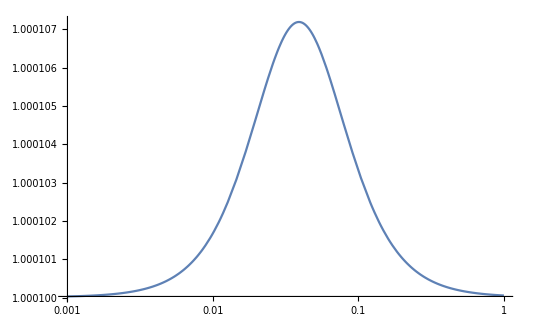

```mathematica
Clear[Om0,H0]
H0=1/2997.92;
Om0=0.281;
fr0 = 0.0001;
LogLinearPlot[mufRalpha[1,k,-fr0]/mufR[1,k,fr0],{k,0.001,1}]
```

#### Check limits

```mathematica
Clear[fR]
```

Large scale limit

```mathematica
Limit[mufRalpha[1,k,0.0001]/.{Om0->1,H0->1},k->0]
Limit[mufR[1,k,0.0001],k->0]
```

0.9999

1.

Small scale limit

```mathematica
FullSimplify[Limit[mufRalpha[1,k,0.0001],k->Infinity]]
Limit[mufR[1,k,0.0001]/.{Om0->1},k->Infinity]
```

1.3332

1.33333

## C) Map between EFTofDE bases to the Horndeski G_i functions as described in Kennedy et al [1705.09290]

KLT makes the following transformations  where κ = 8 π G (compared Eq. 8 of 1606.05339  and Eq. 14 & 15 of 1705.09290)

Λ → -Λ/κ

c →  Γ/(2 κ)

M_2^2 → 2 M_2^2 (Kennedy M22 to Pogosian M22)

X -> 1/2 X  (Kennedy  X to Takushima X)

Possible  sign error in last term of Z function in Table 1 of 1705.09290:  See eq.32 and table 1 of 1705.09290

```mathematica
Clear[M22,M31,c,Λ,aM,aT,aB,aK,Ms,M42, Ω,H]
```

1. Dimensionful to intermediate functions (see Table 1 of 1705.09290 ) up to 1st order in density perturbations

```mathematica
U[ϕ_[t_]]:=-κ Λ[ϕ[t]]+κ c[ϕ[t]]-κ M42[ϕ[t]]/2-κ(9 H[ϕ[t]] M31[ϕ[t]])/8 -M31'[ϕ[t]]/8  +  M22''[ϕ[t]]/(2κ)+(7M22'[ϕ[t]]H[ϕ[t]])/2+ 2 H'[ϕ[t]]M22[ϕ[t]] + 9M22[ϕ[t]] H[ϕ[t]]^2 κ


Z[ϕ_[t_]]:=2 κ c[ϕ[t]] κ^2-2M42[ϕ[t]] κ^3-(3H[ϕ[t]] M31[ϕ[t]])/2 κ^3+M31'[ϕ[t]]/2 κ^2  -2 M22''[ϕ[t]]κ-2 M22'[ϕ[t]]H[ϕ[t]] κ^2+ 8M22[ϕ[t]]H'[ϕ[t]] κ^2

a2[ϕ_[t_]]:=M42[ϕ[t]]/2 κ^4+M31'[ϕ[t]]/8 κ^3-(3H[ϕ[t]] M31[ϕ[t]])/8 κ^4   -  M22''[ϕ[t]]/2 κ^2+(M22'[ϕ[t]]H[ϕ[t]])/2 κ^3+2 κ^3 H'[ϕ[t]]M22[ϕ[t]]-3M22[ϕ[t]] H[ϕ[t]]^2 κ^4

b1[ϕ_[t_]]:= 4M22[ϕ[t]]H[ϕ[t]] κ^3 - 2 M22'[ϕ[t]] κ^2+M31[ϕ [t]]/2 κ^3;  

F[ϕ_[t_]]:=Ω[ϕ[t]]+2 M22[ϕ[t]]κ;

c1[ϕ_[t_]]:=M22[ϕ[t]] κ^2;
```

2. Higher order  functions (see Eq. 21 & 22 of 1705.09290 )

```mathematica
DeltaG2[ϕ_[t_],X_]  := xi23[ϕ[t]](1+X κ^2)^3+xi24[ϕ[t]](1+X κ^2)^4
 DeltaG3[ϕ_[t_],X_]  := xi33[ϕ[t]](1+X κ^2)^3+xi34[ϕ[t]](1+X κ^2)^4
 DeltaG4[ϕ_[t_],X_]  := xi43[ϕ[t]](1+X κ^2)^3+xi44[ϕ[t]](1+X κ^2)^4
 DeltaG5[ϕ_[t_],X_]  := xi53[ϕ[t]](1+X κ^2)^3+xi54[ϕ[t]](1+X κ^2)^4
```

3. α to M : See Chapter B, Sec 2 - we also convert scale factor derivatives to scalar field derivatives : d/da=dt/da dϕ/dt d/dϕ→ 1/aH dϕ/dt d/dϕ & d^2/da^2=1/aH dϕ/dt d/dϕ(1/aH dϕ/dt d/dϕ)→ 1/aH dϕ/dt (-dH/dϕ 1/(a H^2)dϕ/dt d/dϕ-1/a d/dϕ+1/aH(d^2 ϕ)/dt^2 d/dϕ+1/aH dϕ/dt d^2/dϕ^2) where we used da/dϕ= aH dt/dϕ

```mathematica
Clear[M22,M31,c,Λ,aM,aT,aB,aK,Ms,M42, Ω,H]
```

```mathematica
Ω[ϕ_[t_]] := (1+aT[ϕ[t]])Ms[ϕ[t]]κ
M22[ϕ_[t_]]:= -aT[ϕ[t]] Ms[ϕ[t]]
M31[ϕ_[t_]]:= -Ms[ϕ[t]] H[ϕ[t]] (aB[ϕ[t]]+(1+aT[ϕ[t]])aM[ϕ[t]] + ϕ'[t] aT'[ϕ[t]]/H[ϕ[t]])
M42[ϕ_[t_]]:=(H[ϕ[t]]^2 Ms[ϕ[t]] aK[ϕ[t]]-2c[ϕ[t]])/4
Λ[ϕ_[t_]]:=-1/κ ( ϕ'[t] H'[ϕ[t]] (2 Ω[ϕ[t]]+ϕ'[t] Ω'[ϕ[t]]/H[ϕ[t]])+(H[ϕ[t]]^2  3 Ω[ϕ[t]]+(3ϕ'[t] Ω'[ϕ[t]]H[ϕ[t]] +ϕ'[t] (- H'[ϕ[t]]/ H[ϕ[t]]ϕ'[t]Ω'[ϕ[t]] -H[ϕ[t]] Ω'[ϕ[t]]+  ϕ''[t] Ω'[ϕ[t]]+ ϕ'[t] Ω''[ϕ[t]] ) )))
```

4. Set parameters to get Hu-Sawicki linear Poisson modification

```mathematica
aM[ϕ_[t_]]:=ϕ'[t] /((1+ϕ[t])H[ϕ[t]])
aB[ϕ_[t_]]:=-aM[ϕ[t]] 
aK[ϕ_[t_]]:=0
aT[ϕ_[t_]]:=0
Ms[ϕ_[t_]]:=(1+ϕ[t]) / κ 
c[ϕ_[t_]]:=0

xi23[ϕ_[t_]]:=0;
xi24[ϕ_[t_]]:=0;
xi33[ϕ_[t_]]:=0;
xi34[ϕ_[t_]]:=0;
xi43[ϕ_[t_]]:=0;
xi44[ϕ_[t_]]:=0;
xi53[ϕ_[t_]]:=0;
xi54[ϕ_[t_]]:=0;
```

5. Intermediate functions to G functions (see Eq. 17-20 of 1705.09290)

```mathematica
Clear[G2,G3,G4,G5,M1t,M2t,M3t,M1,M2,M3];
G2[ϕ_[t_],X_]:=-U[ϕ[t]]/κ-Z[ϕ[t]]/κ X+4 a2[ϕ[t]] X^2 + DeltaG2[ϕ[t],X]   
G3[ϕ_[t_],X_]:=-2 b1[ϕ[t]] X + DeltaG3 [ϕ[t],X]; 
G4[ϕ_[t_],X_]:=1/(2κ)F[ϕ[t]] +2c1[ϕ[t]]X + DeltaG4[ϕ[t],X];
G5[ϕ_[t_],X_]:=DeltaG5[ϕ[t],X];
```

6. Check linear Poisson modification

```mathematica
M1t[ϕ_[t_]]:=M1 * ((ϕ'[t] a)/(2 H[t]))^2 1/κ
```

```mathematica
FullSimplify[mu[ϕ[t],X,k,a]/. ϕ[t]->0]
```

1+k^2/(3 k^2-a^2 M1)

## D) Testing the PPF non-linear Poisson modification [1608.00522] against exact solutions

```mathematica
Clear["Global`*"];
```

## Define normalised LCDM Hubble and some constants

```mathematica
H0=1/2997.92;
Gnewton = 4.302*10^(-9);
Om = 0.281; 
deltai =(0.00003+0.00012)/2;
H[a_]:= Sqrt[Om/a^3 + 1-Om];
```

```mathematica
scalef = 1;
Mvir = 10^9;
yi = deltai/3;
yf = 1000;
```

## Define the PPF effective Newton’s constant: Eq. 5.3 of 1608.00522

Note we include a parametrisation of p4 to add in an explicit dependency on the model parameter (Ω_rc or f_R0 ) .

```mathematica
y0[a_,yh_,yenv_,Mvir_,par4_,par5_,par6_,par7_,par8_,par9_]:=p4[a,par4,p8[a,par8],p9[a,par9]] a ^p5[a,par5](2 Gnewton H0 Mvir)^p6[a,par6](yenv/yh)^p7[a,par7];
apar[a_,par1_,par3_]:=p1[a,par1]/(p1[a,par1]-1) * p3[a,par3];
xm[a_,yh_,yenv_,Mvir_,par1_,par3_,par4_,par5_,par6_,par7_,par8_,par9_]:=(y0[a,yh,yenv,Mvir,par4,par5,par6,par7,par8,par9]/yh)^apar[a,par1,par3];

Fppf[a_,yh_,yenv_,Mvir_,par1_,par2_,par3_,par4_,par5_,par6_,par7_,par8_,par9_]:=p1[a,par1]*p2[a,par2]*1/xm[a,yh,yenv,Mvir,par1,par3,par4,par5,par6,par7,par8,par9]*((1+xm[a,yh,yenv,Mvir,par1,par3,par4,par5,par6,par7,par8,par9])^(1/p1[a,par1])-1)
```

## Test PPF parameters for DGP

```mathematica
Orc=0.25;
```

### Define exact DGP solution : Eq. C6 of 2005.12184

```mathematica
beta[a_,dof_]:=1+H[a]/Sqrt[dof]*(1+a/3 * H'[a]/H[a])
delta[yh_]:=(1+deltai)/yh^3 -1; 
s3[a_,yh_,dof_]:=2 Om (1+delta[yh])/(9 a^3 beta[a,dof]^2 dof)
```

```mathematica
Fdgp[a_,yh_,dof_]:=2/(3 beta[a,dof]) * (Sqrt[1+s3[a,yh,dof]]-1)/s3[a,yh,dof]
```

### Define PPF parameters : Eq.5.9 of 1608.00522]

```mathematica
p1[a_,dof_]:= 2;
p2[a_,dof_]:= 1/(3 beta[a,dof]);
p3[a_,dof_]:= 3/2;
p4[a_,dof_,dof2_,dof3_]:= 2 Om^(1/3) p2[a,dof]^(2/3) /(4 dof)^(1/3);
p5[a_,dof_]:= -1;
p6[a_,dof_]:= 0;
p7[a_,dof_]:= 0;
p8[a_,dof_]:= 0;
p9[a_,dof_]:= 0;
```

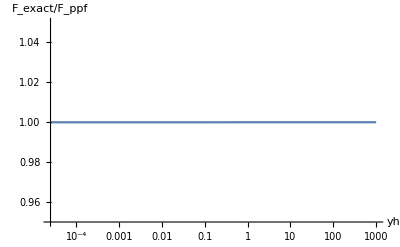

```mathematica
LogLinearPlot[{Fdgp[scalef,yh,Orc]/Fppf[scalef,yh,yh,Mvir,Orc,Orc,Orc,Orc,Orc,Orc,Orc,Orc,Orc]},{yh,yi,yf},PlotRange->{{yi,yf},{0.95,1.05}},AxesLabel->{"yh","F_exact/F_ppf"}]
```

## Test PPF parameters for Hu-Sawicki f(R)

```mathematica
fr0= 0.00001;
```

### Define exact f(R) Hu-Sawicki solution : Eq. C14 of 2005.12184

```mathematica
delta[yh_]:=(1+deltai)/yh^3 -1; 
Rth[Mvir_]:=0.1*(Gnewton*Mvir/(5 Om))^(1/3);
Gtild[a_,y_]:=1/(Om/(y* a)^3 + 4(1-Om))^2;
Of[a_,yh_,yenv_,Mvir_,dof_]:= Abs[dof]/H0^2 yh a (3 Om - 4)^2 * (Gtild[a,yenv] -Gtild[a,yh])/(Rth[Mvir]^2 Om)
```

```mathematica
Ffr[a_,yh_,yenv_,Mvir_,dof_]:=Min[Of[a,yh,yenv,Mvir,dof]-Of[a,yh,yenv,Mvir,dof]^2+Of[a,yh,yenv,Mvir,dof]^3/3,1/3]
Ffr2[a_,yh_,yenv_,Mvir_,dof_]:=Min[Of[a,yh,yenv,Mvir,dof],1/3]
```

```mathematica
Plot3D[{Ffr[scalef,yh,yenv,Mvir,fr0]},{yh,yi,yf},{yenv,yi,yf},AxesLabel->{"yh","ye","F"}]
```

-Graphics3D-

### Find the best fitting PPF parameters with the approximate Chameleon model in Eq.5.6 of 1608.00522 as a guide. Note BD parameter w = 0.

```mathematica
alpha = 0.5;
p1[a_,dof_]:= 3;
p2[a_,dof_]:= 1/3 ;
p3[a_,dof_]:= (4-alpha)/(1-alpha)
p4[a_,dof_,dof2_,dof3_]:=Om^(1/3)*((Om+4*(1-Om))^(-2)*p1[a,dof]*p2[a,dof]/dof)^(1/p3[a,dof]); 
p5[a_,dof_]:=-1;
p6[a_,dof_]:= 2/(3p3[a,dof]); 
p7[a_,dof_]:= 3/(alpha-4); 
p8[a_,dof_]:=1;  
p9[a_,dof_]:=1;
```

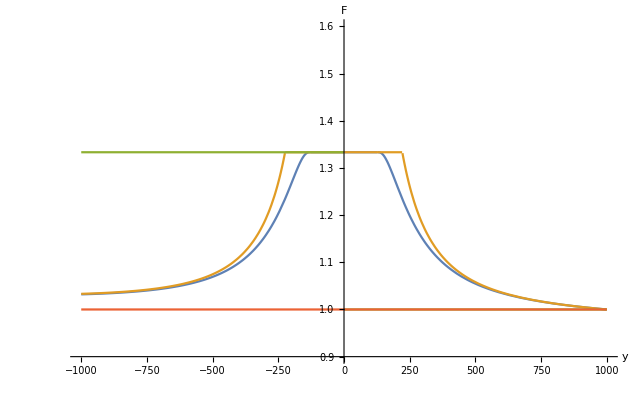

```mathematica
ti = 1;
tm = 0.1;
te=2;
Plot[{1+Ffr[scalef,yh,0.5*yf*te,Mvir*tm, fr0],1+Ffr2[scalef,yh,0.5*yf*te,Mvir*tm, fr0],1+Fppf[scalef,yh,yf*0.5*te,Mvir*tm,fr0,fr0,fr0,fr0,fr0,fr0,fr0,fr0,fr0],1},{yh,-yf,yf},AxesLabel->{"y","F"},PlotRange->{{-yf,yf},{0.9,1.6}}]
```

1

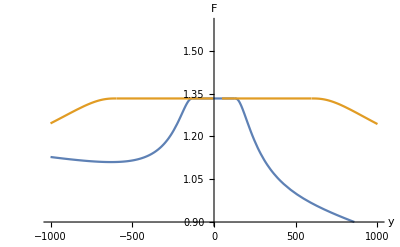

```mathematica
tm = 1
Plot[{1+Ffr[1,yh,0.5*yf*1,Mvir*0.1, fr0],1+Ffr[0.1,yh,0.5*yf*10,Mvir*1, fr0]},{yh,-yf,yf},AxesLabel->{"y","F"},PlotRange->{{-yf,yf},{0.9,1.6}}]
```

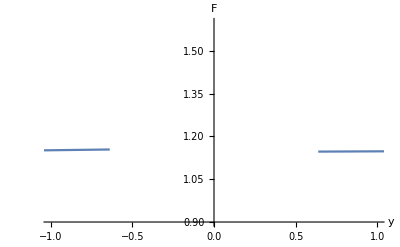

```mathematica
tm = 1;
Plot[{1+Fdgp[1,yh,0.5]},{yh,-yf,yf},AxesLabel->{"y","F"},PlotRange->{{-1,1},{0.9,1.6}}]
```

#### Check fr0 dependency: Create a data set over fr0 values to fit to for fixed yh and yenv

```mathematica
myfrtab=Table[{fr0*i,Ffr[scalef,yf,yi,Mvir,fr0*i]},{i,1,10}]
```

{{0.00001,-2.54399×10^20},{0.00002,-2.0352×10^21},{0.00003,-6.86878×10^21},{0.00004,-1.62816×10^22},{0.00005,-3.17999×10^22},{0.00006,-5.49503×10^22},{0.00007,-8.7259×10^22},{0.00008,-1.30252×10^23},{0.00009,-1.85457×10^23},{0.0001,-2.54399×10^23}}

Set priors

```mathematica
pr3=3;
pr5=3;
pr6=3;
pr7=3;
pr8=3;
pr9=1;
```

```mathematica
sol=FindFit[myfrtab,{Fppf[scalef,yf,yi,Mvir,2,0,par3,fR0,par5,par6,par7,par8,par9],Abs[par3]<pr3,Abs[par5]<pr5,Abs[par6]<pr6,Abs[par7]<pr7,Abs[par9]<pr9,par8>0},{par3,par5,par6,par7,par8,par9},fR0]
```

FindFit::eit: The algorithm does not converge to the tolerance of 1.×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {6.5856×10^-7,2.28109×10^10,1.09762×10^-7}, is returned.

{par3→2.81182,par5→1.23442,par6→2.49955,par7→2.76603,par8→7.77774×10^-11,par9→0.912302}

Check alpha-parametrisation of 1608.00522

```mathematica
p1[a_,dof_]:= dof;
p2[a_,dof_]:= 1/3 ;
p3[a_,dof_]:= (4-dof)/(1-dof);
p4[a_,dof_,dof2_,dof3_]:=Om^(1/3)*((Om+4(1-Om))^(1/(1-dof))*p1[a,dof2]*p2[a,0]/dof3)^p3[a,dof];
p5[a_,dof_]:=-5;
p6[a_,dof_]:= 2/3/p3[a,dof]; 
p7[a_,dof_]:= 3/(dof-4);
p8[a_,dof_]:= dof; 
p9[a_,dof_]:= dof;
```

```mathematica
myp1=5;
sol=FindFit[myfrtab,{Fppf[scalef,yf,yi,Mvir,myp1,0,alpha,alpha,0,alpha,alpha,myp1,fR0],0<alpha<1},{alpha},fR0]
```

{alpha→0.89999}

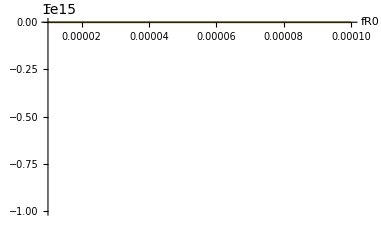

```mathematica
myalpha =1/2;
myp1 = 0.51;
Plot[{Ffr[scalef,yf,yi,Mvir, fR0],Fppf[scalef,yf,yi,Mvir,myp1,0,myalpha,myalpha,0,myalpha,myalpha,myp1,fR0]},{fR0,fr0,fr0*10},AxesLabel->{"fR0","F"}]
```

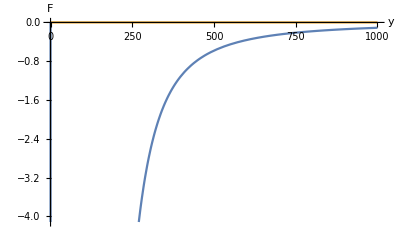

```mathematica
myp1 = 1.5;
Plot[{Ffr[scalef,yh,0.5*yh,Mvir, fr0],Fppf[scalef,yh,0.5*yh,Mvir,myp1,0,myalpha,myalpha,0,myalpha,myalpha,myp1,fr0]},{yh,yi,yf},AxesLabel->{"y","F"}]
```